# Weights Analysis Notebook

## SECTION 1: Functions

```mathematica
(*All other functions needed that are not in the subsections below are defined in the section they're going to be used*)
```

### Variances to Squeezing and nThermal

Calculating the Squeezing and nThermal from a pair of variances VP and VQ from analitic expressions

```mathematica
ClearAll[fVarParameters]

fVarParameters[VarP_,VarQ_]:=Module[{v,vp=VarP,vq=VarQ,s,n},
n = Sqrt[vp*vq]-0.5;
s=Log[Sqrt[vp/vq]]*0.5;
{s,n}
];
```

### Other functions

```mathematica
(*
-> Last Update:  of 08/08/2019 ;
*)
```

```mathematica
Clear[probabilityThermalFock,probabilitySqueezedVacuum,probabilitySumSqueezedVacuum,probabilitySumThermal,probabilitySumPn,probabilitySumPnD,probabilitySumPnPC,probabilityList,probabilityListNormalized,probabilityListTo20,frequencyDistribution,relativeFrequencyDist,probabilitySumList,relativeFreqDistTo20,findVarForSTstate]
```

```mathematica
(* PROBABILITY FUNCTION OF THE THERMAL STATE FOR A FOCK NUMBER  *)
probabilityThermalFock[nThermal_,nFock_] = nThermal^nFock/(1+nThermal)^(nFock+1);

(* PROBABILITY FUNCTION OF THE SQUEEZED VACUUM STATE FOR A FOCK NUMBER :*)
probabilitySqueezedVacuum[Squeezing_,nFock_?EvenQ] := (nFock!)*(Tanh[Squeezing])^(nFock)/( (2^(nFock))*(((nFock/2)!)^2)  * Cosh[Squeezing]);
probabilitySqueezedVacuum[Squeezing_,nFock_?OddQ] =0;
```

```mathematica
(*FUNCTIONS OF SUM OF PROBABILITIES FOR SPECIFIC PARAMETERS*)

(*FOR THE VACUUM STATE EXPRESSION: *)
probabilitySumSqueezedVacuum[Squeezing_]:=Sum[probabilitySqueezedVacuum[Squeezing,nFock],{nFock,0,nFockFinal}];
(*FOR THE THERMAL STATE EXPRESSION: *)
probabilitySumThermal[nThermal_]:=Sum[probabilityThermalFock[nThermal,nFock],{nFock,0,nFockFinal}];
(*FOR THE Pn FUNCTION: *)
probabilitySumPn[Squeezing_,nThermal_]:=Sum[Pn[Squeezing,nThermal,nFock],{nFock,0,nFockFinal}];
(*FOR THE PnDvar FUNCTION: *)
probabilitySumPnD[varp_,varq_]:=Sum[PnDvar[varp,varq,nFock],{nFock,0,nFockFinal}];
(*FOR THE Pn FUNCTION WITH PRECISION CONTROL: *)
probabilitySumPnPC[Squeezing_,nThermal_,PrecisionNumber_]:=Sum[PnPrecisionControl[Squeezing,nThermal,PrecisionNumber,nFock],{nFock,0,nFockFinal}];

(*LIST OF PROBABILITIES FOR A LIMITED RANGE OF FOCK NUMBERS (ITS SUM WILL BE < 1)*)
probabilityList[varp_,varq_,NFockFinal_]:=Chop[Table[PnDvar[varp,varq, nFock],{nFock,0,NFockFinal}]];
(*LIST OF PROBABILITIES FOR A LIMITED RANGE OF FOCK NUMBERS BUT NOW NORMALIZED (ITS SUM WILL BE = 1)*)
probabilityListNormalized[varp_,varq_,NFockFinal_]:=Chop[Table[PnDvar[varp,varq, nFock],{nFock,0,NFockFinal}]]/Sum[PnDvar[varp,varq,nFock],{nFock,0,NFockFinal}];
(*LIST OF PROBABILITIES FOR A LIMITED RANGE OF 20 FOCK NUMBERS WITH THE PROBABILITY OF FINDING NFOCK >20 IN THE LAST ITEM (ITS SUM WILL BE = 1)*)
probabilityListTo20[VarP_,VarQ_,NFockFinal_] :=Module[
{vp=VarP,vq = VarQ,n = NFockFinal,TableTemp,TableSumTemp},

TableTemp = probabilityList[vp,vq,n];
TableSumTemp = Apply[Plus,TableTemp];
 Append[TableTemp,1-TableSumTemp]
];
```

```mathematica
(*FREQUENCY DISTRIBUTION FOR A MULTINOMIAL DIST BASED ON THE NFOCK NUMBERS FROM 0->20 AND THE CHANCE TO GET ANY > 20 (probabilityListTo20) :*)
frequencyDistribution[varp_,varq_,Nmeasure_,NFockFinal_]:= Part[RandomVariate[MultinomialDistribution[Nmeasure,probabilityListTo20[varp,varq,NFockFinal]],1],1];

(*RELATIVE FREQUENCY DISTRIBUTION TO Neasures FOR THE frequencyDistribution LIST :*)
relativeFrequencyDist[varp_,varq_,NMeasure_,NFockFinal_]:= N[Divide[1.,NMeasure]]*frequencyDistribution[varp,varq,NMeasure,NFockFinal];
(*RELATIVE FREQUENCY DISTRIBUTION TO Neasures FOR THE frequencyDistribution LIST, CONSIDERING FOCK NUMBERS 0->20 (THE POSITION 22 IS THE FREQUENCY FOR ANY NFOCK > 20) :*)
relativeFreqDistTo20[varp_,varq_,NMeasure_,NFockFinal_]:= N[Divide[1.,NMeasure]]*Delete[frequencyDistribution[varp,varq,NMeasure,NFockFinal],22];
(*RELATIVE FREQUENCY DISTRIBUTION TO Neasures FOR THE frequencyDistribution LIST, CONSIDERING FOCK NUMBERS 0->NFockFinal (THE POSITION NFockFinal+2 IS THE FREQUENCY FOR ANY NFOCK > NFockFinal) :*)
relativeFreqDistToN[varp_,varq_,NMeasure_,NFockFinal_]:= N[Divide[1.,NMeasure]]*Delete[frequencyDistribution[varp,varq,NMeasure,NFockFinal],NFockFinal+2];

(*SUM OF PROBABILITIES OF THE LIST probabilityList:*)
probabilitySumList[varp_,varq_,NFockFinal_]:=Apply[Plus,probabilityList[varp,varq,NFockFinal]];
```

```mathematica
(*Function to save data to the notebook got from Szabolcs Horvát's blog in 08/18/2019.
http://szhorvat.net/pelican/save-data-in-notebooks.html

With this function the datasets can be saved inside cells in the notebook instead of saving in datafiles. 
This way there is no need to import/export data. 

Used a lot!! Thanks Szabolcs!
*)

ClearAll[SaveToCell]

SaveToCell::usage =
    "SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n" <>
    "SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell, HoldFirst]
SaveToCell[var_, name : Except[_?OptionQ] : "data", opt : OptionsPattern[]] :=
    With[{data = Compress[var],
      panel = ToBoxes@Tooltip[Panel[name, FrameMargins -> Small], DateString[]]},
      CellPrint@Cell[
        BoxData@RowBox[{
          MakeBoxes[var],
          "=",
          InterpretationBox[panel, Uncompress[data]],
          ";"
        }],
        "Input",
        GeneratedCell -> False, (* prevent deletion by Cell > Delete All Output: *)
        CellLabel -> "(saved)",
        opt,
        CellLabelAutoDelete -> False
      ]
    ];
```

### Pn Dodonov Functions

```mathematica
(*
Modified 07-08-2019
-> Explicit form for PnDvar. 
Probability function of a squeezed thermal state on the Fock states based on 
the work     ; 
Photon distribution for one-mode mixed light with a generic Gaussian Wigner function
    V.V.Dodonov,O.V.Man’ko,and V.I.Man’ko
    Phys.Rev.A 49,2993–Published 1 April 1994
    https://doi.org/10.1103/PhysRevA.49.2993
*)

Clear[T,d,σpp ,σqq,σpq,Squeezing,P0,nFock,nThermal,PnD,H0,H0Td,PnDTd,P0Td,TraceV,detV]
Unprotect[Power];
Power[0,0] = 1;
(*The Variance Matrix is defined below*)
σqq[Squeezing_,nThermal_] =(2*nThermal +1)*Exp[-2Squeezing]/2;
σpp[Squeezing_,nThermal_]  = (2*nThermal +1)*Exp[2Squeezing]/2;
σpq=0;

(* The important functions needed are expressed in terms of d (determinant) and T (trace) of the variance matrix like equations 3 and 4:  *)
d [ σpp_,σqq_]= σpp*σqq - (σpq )^2;
T[ σpp_,σqq_] = σpp +σqq; 
(*But we also need d and T as functions of Squeezing and nThermal. So we rewrite these functions as: *)
detST[Squeezing_,nThermal_]= σpp[Squeezing,nThermal]*σqq[Squeezing,nThermal]- (σpq )^2;
traceST[ Squeezing_,nThermal_] = σpp[Squeezing,nThermal] +σqq[Squeezing,nThermal];

(*****)
(*We have no displacement:*)
qDisplaced = 0;
pDisplaced = 0;
(*****)

(* For the case of no displacement the Hermite polynomial is written in the special form of equation 23, using equation 22 too: *)

H0[Squeezing_,nThermal_,nFock_] = Re[Factorial[nFock]*( (-(T[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]-2*d[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]-0.5)/(T[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]+2*d[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]+0.5))^(nFock/2) )*LegendreP[nFock,-((1-4*d[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]])/(1+2*T[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]+4*d[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]))/( (-(T[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]-2*d[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]-0.5)/(T[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]+2*d[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]+0.5))^(1/2) )]];

(*If you want to use the probability distribution as a function of the Trace(T) and the Determinant(d) of the Variance Matrix you
use H0Td = H0[T,d,nFock]:*)

H0Td[TraceV_,detV_,nFock_] :=Re[( (-(TraceV-2*detV-0.5)/(TraceV+2*detV+0.5))^(nFock/2) )*LegendreP[nFock,-((1-4*detV)/(1+2*TraceV+4*detV))/( (-(TraceV-2*detV-0.5)/(TraceV+2*detV+0.5))^(1/2) )]] ;
(*The probability function for nFock = 0 is given by equation 12 : *)

P0[nThermal_,Squeezing_] = Exp[(-(pDisplaced^2)*(2*σqq[Squeezing,nThermal] +1)-(qDisplaced^2)*(2*σpp[Squeezing,nThermal] +1)+(qDisplaced)*(pDisplaced)*4*σpq)/(1+2*T[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]+4*d[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]])]/( (d[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]+0.5*T[σpp[Squeezing,nThermal],σqq[Squeezing,nThermal]]+0.25)^(1/2) );

(*And as a function of T and d:*)

P0Td[TraceV_,detV_] = Exp[(-(pDisplaced^2)*(2*σqq +1)-(qDisplaced^2)*(2*σpp +1)+(qDisplaced)*(pDisplaced)*4*σpq)/(1+2*TraceV+4*detV)]/( (detV+0.5*TraceV+0.25)^(1/2) );

(*The probability distribution desired is given by equation 14, considering (y1,y2)=(0,0). Because of this the Hermite polynomials are
given by equation 23. *)

PnD[Squeezing_,nThermal_,nFock_] :=P0[nThermal,Squeezing]*H0[Squeezing,nThermal,nFock]/Factorial[nFock];
(*For the same distribution but as function of T and d: *)
(*Here TraceV = 1 and detV = 1/4 means zero Squeezing and zero nThermal. The limit of the fraction inside the Legendre function when detV->0 is 0. But Mathematica reads it as 0/0. To avoid this
problem we write the fuction as follows:  *)
PnDTd[TraceV_/;TraceV!=1,detV_/;detV!=1/4,nFock_] :=H0Td[TraceV,detV,nFock] *P0Td[TraceV,detV] ;
PnDTd[TraceV_/;TraceV==1,detV_/;detV==1/4,nFock_/;nFock==0] :=1;
PnDTd[TraceV_/;TraceV==1,detV_/;detV==1/4,nFock_/;nFock>0] :=0;

(*Writing the PnD as a function of the variances of q and p: PnDvar:*)

Clear[P0var,H0var,PnDvar]

H0var[VARP_,VARQ_,nFock_] = H0Td[T[VARP,VARQ],d[VARP,VARQ],nFock];

P0var[VARP_,VARQ_] = P0Td[T[VARP,VARQ],d[VARP,VARQ]];

PnDvar[σpp_/;σpp!=1/2,σqq_/;σqq!=1/2,nFock_] :=H0var[σpp,σqq,nFock] *P0var[σpp,σqq] ;
PnDvar[σpp_/;σpp==1/2,σqq_/;σqq==1/2,nFock_/;nFock==0] :=1;
PnDvar[σpp_/;σpp==1/2,σqq_/;σqq==1/2,nFock_/;nFock>0] :=0;

Protect[Power];
```

### Pn Functions

```mathematica
(*
Pn functions for n = 0, ... , 20 obtained by solving the overlap integral between the Wigner ;
functions of a general gaussian state and of the Fock state n. For each n we asked Mathematica to 
solve the integral and obtained the results below.
*)
```

```mathematica
Pn[Squeezing0_,nThermal0_,0]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr}, 2/((1+2 nThermal) Sqrt[1+1/(1+2 nThermal)^2+(2 Cosh[2 Squeezing])/(1+2 nThermal)])]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,1]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},(8 E^(3 Squeezing) nThermal (1+nThermal))/((1+E^(2 Squeezing)+2 nThermal) (1+E^(2 Squeezing) (1+2 nThermal)))^(3/2)]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,2]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},(2 E^(5 Squeezing) (-1-4 nThermal+12 nThermal^2+32 nThermal^3+16 nThermal^4+(1+2 nThermal)^2 Cosh[4 Squeezing]))/((1+E^(2 Squeezing)+2 nThermal) (1+E^(2 Squeezing) (1+2 nThermal)))^(5/2)]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,3]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},(8 nThermal (1+nThermal) (-3+4 nThermal (-3+nThermal (1+4 nThermal (2+nThermal)))+3 (1+2 nThermal)^2 Cosh[4 Squeezing]))/((1+E^(-2 Squeezing)+2 nThermal) (1+E^(2 Squeezing)+2 nThermal))^(7/2)]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,4]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},(3 (1+2 nThermal)^4+3 E^(16 Squeezing) (1+2 nThermal)^4+12 E^(4 Squeezing) (1+2 nThermal)^2 (-1-4 nThermal+28 nThermal^2+64 nThermal^3+32 nThermal^4)+12 E^(12 Squeezing) (1+2 nThermal)^2 (-1-4 nThermal+28 nThermal^2+64 nThermal^3+32 nThermal^4)+2 E^(8 Squeezing) (9+72 nThermal-168 nThermal^2-2016 nThermal^3-3824 nThermal^4-512 nThermal^5+4608 nThermal^6+4096 nThermal^7+1024 nThermal^8))/(4 Sqrt[1+E^(-2 Squeezing)+2 nThermal] (1+E^(2 Squeezing)+2 nThermal)^(9/2) (1+E^(2 Squeezing) (1+2 nThermal))^4)]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,5]:= Module[{Squeezing,nThermal,Pr = 100},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/((1+E^(-2 Squeezing)+2 nThermal) (1+E^(2 Squeezing)+2 nThermal))^(11/2) E^(-8 Squeezing) nThermal (1+nThermal) (15 (1+2 nThermal)^4+15 E^(16 Squeezing) (1+2 nThermal)^4+20 E^(4 Squeezing) (1+2 nThermal)^2 (-3-12 nThermal+20 nThermal^2+64 nThermal^3+32 nThermal^4)+20 E^(12 Squeezing) (1+2 nThermal)^2 (-3-12 nThermal+20 nThermal^2+64 nThermal^3+32 nThermal^4)+2 E^(8 Squeezing) (45+360 nThermal+440 nThermal^2-2400 nThermal^3-6576 nThermal^4-3584 nThermal^5+3584 nThermal^6+4096 nThermal^7+1024 nThermal^8))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,6]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(8 ((1+E^(-2 Squeezing)+2 nThermal) (1+E^(2 Squeezing)+2 nThermal))^(13/2)) E^(-12 Squeezing) (5 (1+2 nThermal)^6+5 E^(24 Squeezing) (1+2 nThermal)^6+30 E^(4 Squeezing) (1+2 nThermal)^4 (-1-4 nThermal+44 nThermal^2+96 nThermal^3+48 nThermal^4)+30 E^(20 Squeezing) (1+2 nThermal)^4 (-1-4 nThermal+44 nThermal^2+96 nThermal^3+48 nThermal^4)+15 E^(8 Squeezing) (1+2 nThermal)^2 (5+40 nThermal-264 nThermal^2-2144 nThermal^3-2864 nThermal^4+3584 nThermal^5+10752 nThermal^6+8192 nThermal^7+2048 nThermal^8)+15 E^(16 Squeezing) (1+2 nThermal)^2 (5+40 nThermal-264 nThermal^2-2144 nThermal^3-2864 nThermal^4+3584 nThermal^5+10752 nThermal^6+8192 nThermal^7+2048 nThermal^8)+4 E^(12 Squeezing) (-25-300 nThermal+660 nThermal^2+17600 nThermal^3+67200 nThermal^4+62400 nThermal^5-159936 nThermal^6-439296 nThermal^7-349440 nThermal^8+20480 nThermal^9+184320 nThermal^10+98304 nThermal^11+16384 nThermal^12))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,7]:= Module[{Squeezing,nThermal,Pr = 90},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(1260 (1+2 nThermal) Sqrt[π]) ((1+2 nThermal)/(1+E^(-2 Squeezing)+2 nThermal))^(15/2) (135135/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(509355 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(72765 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(416745 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(138915 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(59535 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(2 (1+2 nThermal)^2)-(385875 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(231525 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(231525 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(2 (1+2 nThermal)^3)+(55125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(2 (1+2 nThermal)^3)+(220500 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(220500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(198450 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(110250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(55125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(2 (1+2 nThermal)^4)-(79380 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(132300 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(198450 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(198450 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(231525 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(2 (1+2 nThermal)^5)+(59535 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(2 (1+2 nThermal)^5)+(17640 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(52920 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(132300 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(220500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(231525 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(138915 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(72765 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(2 (1+2 nThermal)^6)-(2520 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(17640 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(79380 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(220500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(385875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(416745 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(509355 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(2 (1+2 nThermal)^7)+(135135 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(2 (1+2 nThermal)^7))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,8]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(10080 (1+2 nThermal) Sqrt[π]) ((1+2 nThermal)/(1+E^(-2 Squeezing)+2 nThermal))^(17/2) (2027025/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(4324320 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(540540 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(8149680 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(2328480 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(436590 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(8890560 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(4445280 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(1905120 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(396900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(6174000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(4939200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(3704400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(1764000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(385875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(2822400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(3528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(4233600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(3528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(1764000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(396900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(846720 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(1693440 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(3175200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(4233600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(3704400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(1905120 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(436590 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(161280 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(564480 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(1693440 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(3528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(4939200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(4445280 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(2328480 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(540540 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(20160 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(161280 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(846720 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(2822400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(6174000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(8890560 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(8149680 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(4324320 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(2027025 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(2 (1+2 nThermal)^8))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,9]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(90720 (1+2 nThermal) Sqrt[π]) ((1+2 nThermal)/(1+E^(-2 Squeezing)+2 nThermal))^(19/2) (34459425/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(164189025 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(18243225 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(175134960 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(43783740 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(7297290 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(220041360 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(94303440 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(35363790 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(6548850 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(180033840 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(120022560 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(77157360 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(32148900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(6251175 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(100018800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(100018800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(100018800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(71442000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(31255875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(6251175 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(38102400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(57153600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(85730400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(95256000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(71442000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(32148900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(6548850 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(9797760 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(22861440 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(51438240 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(85730400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(100018800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(77157360 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(35363790 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(7297290 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1632960 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(6531840 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(22861440 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(57153600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(100018800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(120022560 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(94303440 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(43783740 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(18243225 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(2 (1+2 nThermal)^8)-(181440 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(1632960 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(9797760 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(38102400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(100018800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(180033840 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(220041360 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(175134960 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(164189025 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(2 (1+2 nThermal)^9)+(34459425 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(2 (1+2 nThermal)^9))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,10]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(907200 (1+2 nThermal) Sqrt[π]) ((1+2 nThermal)/(1+E^(-2 Squeezing)+2 nThermal))^(21/2) (654729075/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(1722971250 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(172297125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(4104725625 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(912161250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(273648375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(2 (1+2 nThermal)^2)-(5837832000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(2189187000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(729729000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(121621500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(5501034000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(3143448000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(1768189500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(654885000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(114604875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(3600676800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(3000564000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(2571912000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(1607445000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(625117500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(112521150 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(1666980000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(2000376000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(2500470000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(2381400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(1562793750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(625117500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(114604875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(544320000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(952560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(1714608000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(2381400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(2381400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1607445000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(654885000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(121621500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(122472000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(326592000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(857304000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(1714608000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(2500470000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(2571912000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(1768189500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(729729000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(273648375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(2 (1+2 nThermal)^8)-(18144000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(81648000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(326592000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(952560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(2000376000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(3000564000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(3143448000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(2189187000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(912161250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(172297125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(1814400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(18144000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(122472000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(544320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(1666980000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(3600676800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(5501034000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(5837832000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(4104725625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(1722971250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(654729075 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(2 (1+2 nThermal)^10))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,11]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(9979200 (1+2 nThermal) Sqrt[π]) E^(23 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(23/2) (13749310575/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(79222218075 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(7202019825 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(104239760625 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(20847952125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(5685805125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(2 (1+2 nThermal)^2)-(165557266875 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(55185755625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(33111453375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(2 (1+2 nThermal)^3)+(5016886875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(2 (1+2 nThermal)^3)+(176594418000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(88297209000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(44148604500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(14716201500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(2341213875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(133125022800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(95089302000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(71316976500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(39620542500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(13867189875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(2269176525 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(72613648800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(72613648800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(77800338000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(64833615000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(37819608750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(13615059150 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(2269176525 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(28814940000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(40340916000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(60511374000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(72037350000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(63032681250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(37819608750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(13867189875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(2341213875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(8232840000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(16465680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(34577928000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(57629880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(72037350000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(64833615000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(39620542500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(14716201500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(5016886875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(2 (1+2 nThermal)^8)-(1646568000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(4939704000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(14819112000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(34577928000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(60511374000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(77800338000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(71316976500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(44148604500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(33111453375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(2 (1+2 nThermal)^9)+(5685805125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(2 (1+2 nThermal)^9)+(219542400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(1097712000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(4939704000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(16465680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(40340916000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(72613648800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(95089302000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(88297209000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(55185755625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(20847952125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(7202019825 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(2 (1+2 nThermal)^10)-(19958400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(219542400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(1646568000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(8232840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(28814940000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(72613648800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(133125022800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(176594418000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(165557266875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(104239760625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(79222218075 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(2 (1+2 nThermal)^11)+(13749310575 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(2 (1+2 nThermal)^11))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,12]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(119750400 (1+2 nThermal) Sqrt[π]) E^(25 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(25/2) (316234143225/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(989950361400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(82495863450 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(2851999850700 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(518545427400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(64818178425 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(5003508510000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(1501052553000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(409377969000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(56858051250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(5960061607500 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(2648916270000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(1192012321500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(361215855000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(105354624375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(2 (1+2 nThermal)^4)-(5085919238400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(3178699524000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(2119133016000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(1059566508000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(337134798000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(50570219700 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(3195000547200 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(2738571897600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(2567411154000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(1901786040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(998437671000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(326761419600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(49921883550 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(1493766489600 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1742727571200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(2240649734400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(2334010140000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(1815341220000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(980284258800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(326761419600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(50570219700 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(518668920000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(829870272000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(1452272976000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(2074675680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(2269176525000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(1815341220000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(998437671000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(337134798000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(105354624375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(2 (1+2 nThermal)^8)-(131725440000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(296382240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(711317376000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(1383117120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(2074675680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(2334010140000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(1901786040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(1059566508000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(361215855000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(56858051250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(23710579200 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(79035264000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(266744016000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(711317376000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(1452272976000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(2240649734400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(2567411154000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(2119133016000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(1192012321500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(409377969000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(64818178425 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(2874009600 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(15807052800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(79035264000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(296382240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(829870272000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(1742727571200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(2738571897600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(3178699524000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(2648916270000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(1501052553000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(518545427400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(82495863450 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(239500800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(2874009600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(23710579200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(131725440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(518668920000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(1493766489600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(3195000547200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(5085919238400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(5960061607500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(5003508510000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(2851999850700 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(989950361400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(316234143225 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(2 (1+2 nThermal)^12))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,13]:= Module[{Squeezing,nThermal,Pr = 90},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(1556755200 (1+2 nThermal) Sqrt[π]) E^(27 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(27/2) (7905853580625/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(53443570205025 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(4111043861925 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(83650805538300 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(13941800923050 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(1608669337275 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(160662658256100 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(43817088615300 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(10954272153825 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(1404393865875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(211398234547500 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(84559293819000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(34592438380500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(9609010661250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(2587041331875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(2 (1+2 nThermal)^4)-(201450082333500 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(111916712407500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(67150027444500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(30522739747500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(17804931519375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(2 (1+2 nThermal)^5)+(2465298210375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(2 (1+2 nThermal)^5)+(143253391881600 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(107440043911200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(89533369926000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(59688913284000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(28487890431000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(8546367129300 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(1205256902850 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(77136441782400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(77136441782400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(86778497005200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(80350460190000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(56245322133000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(27611339956200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(8436798319950 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1205256902850 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(31555817092800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(42074422790400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(63111634185600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(78889542732000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(76698166545000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(55222679912400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(27611339956200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(8546367129300 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(2465298210375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(2 (1+2 nThermal)^8)-(9739449720000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(17531009496000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(35062018992000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(58436698320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(76698166545000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(76698166545000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(56245322133000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(28487890431000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(17804931519375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(2 (1+2 nThermal)^9)+(2587041331875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(2 (1+2 nThermal)^9)+(2226159936000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(5565399840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(15026579568000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(33392399040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(58436698320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(78889542732000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(80350460190000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(59688913284000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(30522739747500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(9609010661250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(1404393865875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(364280716800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(1335695961600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(5008859856000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(15026579568000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(35062018992000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(63111634185600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(86778497005200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(89533369926000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(67150027444500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(34592438380500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(10954272153825 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(1608669337275 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(40475635200 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(242853811200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(1335695961600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(5565399840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(17531009496000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(42074422790400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(77136441782400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(107440043911200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(111916712407500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(84559293819000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(43817088615300 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(13941800923050 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(4111043861925 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(2 (1+2 nThermal)^12)-(3113510400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(40475635200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(364280716800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(2226159936000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(9739449720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(31555817092800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(77136441782400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(143253391881600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(201450082333500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(211398234547500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(160662658256100 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(83650805538300 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(53443570205025 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(2 (1+2 nThermal)^13)+(7905853580625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(2 (1+2 nThermal)^13))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,14]:= Module[{Squeezing,nThermal,Pr = 70},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(21794572800 (1+2 nThermal) Sqrt[π]) E^(29 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(29/2) (213458046676875/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(774773650901250 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(55340975064375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(2618734940046225 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(402882298468650 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(86331921100425 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(2 (1+2 nThermal)^2)-(5465185961835600 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(1366296490458900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(315299190105900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(37535617869750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(7872470254548900 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(2862716456199600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(1073518671074850 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(275261197711500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(68815299427875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(2 (1+2 nThermal)^4)-(8286810794262000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(4143405397131000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(2260039307526000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(941683044802500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(253530050523750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(32596720781625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(6580702689561000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(4387135126374000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(3290351344780500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(1994152330170000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(872441644449375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(241599224616750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(63275987399625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(2 (1+2 nThermal)^6)-(4011094972684800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(3509708101099200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(3509708101099200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(2924756750916000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(1861208841492000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(837543978671400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(236230352958600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(31336679474100 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1889842823668800 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(2159820369907200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(2834764235503200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(3149738039448000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(2756020784517000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(1803940877138400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(826806235355100 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(236230352958600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(63275987399625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(2 (1+2 nThermal)^8)-(687215572243200 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(1030823358364800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(1767125757196800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(2577058395912000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(3006568128564000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(2705911315707600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(1803940877138400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(837543978671400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(241599224616750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(32596720781625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(190893214512000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(381786429024000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(859019465304000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(1636227552960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(2505473440470000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(3006568128564000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(2756020784517000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(1861208841492000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(872441644449375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(253530050523750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(68815299427875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(2 (1+2 nThermal)^10)-(39666122496000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(109081836864000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(327245510592000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(818113776480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(1636227552960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(2577058395912000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(3149738039448000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(2924756750916000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(1994152330170000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(941683044802500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(275261197711500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(37535617869750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(5949918374400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(23799673497600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(98173653177600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(327245510592000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(859019465304000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(1767125757196800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(2834764235503200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(3509708101099200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(3290351344780500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(2260039307526000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(1073518671074850 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(315299190105900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(86331921100425 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(2 (1+2 nThermal)^12)-(610248038400 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(3966612249600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(23799673497600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(109081836864000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(381786429024000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(1030823358364800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(2159820369907200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(3509708101099200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(4387135126374000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(4143405397131000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(2862716456199600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(1366296490458900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(402882298468650 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(55340975064375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(43589145600 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(610248038400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(5949918374400 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(39666122496000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(190893214512000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(687215572243200 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(1889842823668800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(4011094972684800 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(6580702689561000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(8286810794262000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(7872470254548900 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(5465185961835600 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(2618734940046225 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(774773650901250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(213458046676875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(2 (1+2 nThermal)^14))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,15]:= Module[{Squeezing,nThermal,Pr = 90},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(326918592000 (1+2 nThermal) Sqrt[π]) E^(31 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(31/2) (6190283353629375/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(48028060502296875 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(3201870700153125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(87162035726390625 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(12451719389484375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(2490343877896875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(2 (1+2 nThermal)^2)-(196405120503466875 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(45324258577723125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(19424682247595625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(2 (1+2 nThermal)^3)+(2158298027510625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(2 (1+2 nThermal)^3)+(307416710353252500 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(102472236784417500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(35471158886913750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(8445514020693750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(1970619938161875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(2 (1+2 nThermal)^4)-(354261161454700500 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(161027800661227500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(80513900330613750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(30966884742543750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(15483442371271875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(2 (1+2 nThermal)^5)+(1858013084552625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(2 (1+2 nThermal)^5)+(310755404784825000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(186453242870895000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(127127211048337500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(70626228360187500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(28522130683921875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(7334262175865625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(1792819642989375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(2 (1+2 nThermal)^6)-(211522586450175000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(164517567239025000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(148065810515122500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(112171068572062500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(65433123333703125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(27179912769384375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(14237097164915625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(2 (1+2 nThermal)^7)+(1762688220418125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(2 (1+2 nThermal)^7)+(112812046106760000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(112812046106760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(131614053791220000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(131614053791220000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(104692997333925000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(62815798400355000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(26575914707842500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(7050752881672500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(1762688220418125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(2 (1+2 nThermal)^8)-(47246070591720000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(60744947903640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(91117421855460000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(118115176479300000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(124020935303265000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(101471674339035000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(62010467651632500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(26575914707842500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(14237097164915625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(2 (1+2 nThermal)^9)+(1792819642989375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(2 (1+2 nThermal)^9)+(15462350375472000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(25770583959120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(49700411921160000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(82834019868600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(112746304821150000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(121766009206842000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(101471674339035000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(62815798400355000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(27179912769384375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(7334262175865625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(1858013084552625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(2 (1+2 nThermal)^10)-(3904633933200000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(8590194653040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(21475486632600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(46018899927000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(80533074872250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(112746304821150000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(124020935303265000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(104692997333925000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(65433123333703125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(28522130683921875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(15483442371271875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(2 (1+2 nThermal)^11)+(1970619938161875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(2 (1+2 nThermal)^11)+(743739796800000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(2231219390400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(7363023988320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(20452844412000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(46018899927000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(82834019868600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(118115176479300000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(131614053791220000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(112171068572062500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(70626228360187500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(30966884742543750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(8445514020693750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(2158298027510625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(2 (1+2 nThermal)^12)-(102979356480000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(446243878080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(2008097451360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(7363023988320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(21475486632600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(49700411921160000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(91117421855460000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(131614053791220000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(148065810515122500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(127127211048337500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(80513900330613750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(35471158886913750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(19424682247595625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(2 (1+2 nThermal)^13)+(2490343877896875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(2 (1+2 nThermal)^13)+(9807557760000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(68652904320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(446243878080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(2231219390400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(8590194653040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(25770583959120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(60744947903640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(112812046106760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(164517567239025000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(186453242870895000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(161027800661227500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(102472236784417500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(45324258577723125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(12451719389484375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(3201870700153125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(2 (1+2 nThermal)^14)-(653837184000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(9807557760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(102979356480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(743739796800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(3904633933200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(15462350375472000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(47246070591720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(112812046106760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(211522586450175000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(310755404784825000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(354261161454700500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(307416710353252500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(196405120503466875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(87162035726390625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(48028060502296875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(2 (1+2 nThermal)^15)+(6190283353629375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(2 (1+2 nThermal)^15))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,16]:= Module[{Squeezing,nThermal,Pr = 90},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(5230697472000 (1+2 nThermal) Sqrt[π]) E^(33 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(33/2) (191898783962510625/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(792356269264560000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(49522266829035000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(3073795872147000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(409839449619600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(38422448401837500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(7437827048652000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(1593820081854000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(318764016370800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(33204585038625000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(12569927712221880000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(3867670065299040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(1243179663846120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(276262147521360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(30216172385148750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(15739735570086528000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(6558223154202720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(3026872225016640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(1081025794648800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(252239352084720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(28376927109531000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(15115142888733888000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(8244623393854848000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(5152889621159280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(2642507498030400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(990940311761400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(237825674822736000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(27250858573438500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(11364769089273600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(7955338362491520000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(6508913205674880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(4520078615052000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(2433888485028000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(938785558510800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(229480914302640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(26636177552985000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(6768722766405600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(6016642459027200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(6317474581978560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(5743158710889600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(4187719893357000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(2319352556320800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(911174218554600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(225624092213520000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(26440323306271875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(3208875978147840000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(3609985475416320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(4813313967221760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(5615532961758720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(5360281463496960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(4020211097622720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(2267811388402560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(902496368854080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(225624092213520000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(26636177552985000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(1209499407148032000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(1727856295925760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(2915757499374720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(4319640739814400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(5291559906272640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(5195349726158592000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(3968669929704480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(2267811388402560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(911174218554600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(229480914302640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(27250858573438500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(359851063283712000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(659726949353472000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(1413700605757440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(2650688635795200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(4123293433459200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(5195349726158592000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(5195349726158592000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(4020211097622720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(2319352556320800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(938785558510800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(237825674822736000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(28376927109531000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(83298857241600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(199917257379840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(549772457794560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(1308982042368000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(2577058395912000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(4123293433459200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(5291559906272640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(5360281463496960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(4187719893357000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(2433888485028000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(990940311761400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(252239352084720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(30216172385148750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(14645952921600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(47599346995200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(171357649182720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(523592816947200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(1308982042368000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(2650688635795200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(4319640739814400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(5615532961758720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(5743158710889600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(4520078615052000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(2642507498030400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(1081025794648800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(276262147521360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(33204585038625000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(1883051089920000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(8787571752960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(42839412295680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(171357649182720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(549772457794560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(1413700605757440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(2915757499374720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(4813313967221760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(6317474581978560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(6508913205674880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(5152889621159280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(3026872225016640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(1243179663846120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(318764016370800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(38422448401837500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(167382319104000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(1255367393280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(8787571752960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(47599346995200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(199917257379840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(659726949353472000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(1727856295925760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(3609985475416320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(6016642459027200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(7955338362491520000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(8244623393854848000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(6558223154202720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(3867670065299040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(1593820081854000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(409839449619600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(49522266829035000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(10461394944000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(167382319104000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(1883051089920000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(14645952921600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(83298857241600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(359851063283712000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(1209499407148032000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(3208875978147840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(6768722766405600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(11364769089273600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(15115142888733888000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(15739735570086528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(12569927712221880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(7437827048652000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(3073795872147000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(792356269264560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(191898783962510625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(2 (1+2 nThermal)^16))
]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,17]:= Module[{Squeezing,nThermal,Pr = 90},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(88921857024000 (1+2 nThermal) Sqrt[π]) E^(35 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(35/2) (6332659870762850625/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(55458748565165570625 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(3262279327362680625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(114495480908728920000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(14311935113591115000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(1262817804140392500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(296109002350161000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(59221800470032200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(11104087588131037500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(1088636038052062500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(537383004265107000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(153538001218602000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(46061400365580600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(9596125076162625000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(987836404899093750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(726541821766424664000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(279439162217855640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(119759640950509560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(39919880316836520000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(8732473819307988750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(924614874985551750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(758130596625834432000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(379065298312917216000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(218691518257452240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(104138818217834400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(36448586376242040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(8200931934654459000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(884414228247049500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(624039470692013376000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(397116026804008512000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(297837020103006384000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(190921166732696400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(95460583366348200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(34365810011885352000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(7875498127723726500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(860348534961415500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(410552283350008800000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(328441826680007040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(313512652740006720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(261260543950005600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(175848443043273000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(90436342136540400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(33159992116731480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(7697855312812665000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(849028159501396875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(217351208832357600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(217351208832357600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(260821450598829120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(276628811241182400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(242050209836034600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(167573222194177800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(87776449720759800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(32602681324853640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(7641253435512571875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(849028159501396875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(92736515768472576000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(115920644710590720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(173880967065886080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(231841289421181440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(258186890491770240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(232368201442593216000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(163849372812084960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(86940483532943040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(32602681324853640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(7697855312812665000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(860348534961415500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(31776848060525568000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(49935046952254464000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(93628213035477120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(156047021725795200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(218465830416113280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(250242678476638848000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(229389121936918944000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(163849372812084960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(87776449720759800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(33159992116731480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(7875498127723726500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(884414228247049500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(8666413107416064000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(17332826214832128000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(40855947506390016000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(85116557304979200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(148953975283713600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(214493724408547584000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(250242678476638848000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(232368201442593216000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(167573222194177800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(90436342136540400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(34365810011885352000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(8200931934654459000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(924614874985551750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(1851797672524800000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(4814673948564480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(14444021845693440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(37829581024435200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(82752208490952000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(148953975283713600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(218465830416113280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(258186890491770240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(242050209836034600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(175848443043273000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(95460583366348200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(36448586376242040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(8732473819307988750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(987836404899093750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(302334313881600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(1058170098585600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(4126863384483840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(13756211281612800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(37829581024435200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(85116557304979200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(156047021725795200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(231841289421181440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(276628811241182400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(261260543950005600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(190921166732696400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(104138818217834400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(39919880316836520000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(9596125076162625000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(1088636038052062500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(36280117665792000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(181400588328960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(952353088727040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(4126863384483840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(14444021845693440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(40855947506390016000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(93628213035477120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(173880967065886080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(260821450598829120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(313512652740006720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(297837020103006384000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(218691518257452240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(119759640950509560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(46061400365580600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(11104087588131037500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(1262817804140392500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(3023343138816000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(24186745110528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(181400588328960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(1058170098585600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(4814673948564480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(17332826214832128000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(49935046952254464000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(115920644710590720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(217351208832357600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(328441826680007040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(397116026804008512000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(379065298312917216000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(279439162217855640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(153538001218602000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(59221800470032200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(14311935113591115000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(3262279327362680625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(2 (1+2 nThermal)^16)-(177843714048000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(3023343138816000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(36280117665792000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(302334313881600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(1851797672524800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(8666413107416064000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(31776848060525568000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(92736515768472576000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(217351208832357600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(410552283350008800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(624039470692013376000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(758130596625834432000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(726541821766424664000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(537383004265107000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(296109002350161000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(114495480908728920000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(55458748565165570625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(2 (1+2 nThermal)^17)+(6332659870762850625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(2 (1+2 nThermal)^17))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,18]:= Module[{Squeezing,nThermal,Pr = 90},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(1600593426432000 (1+2 nThermal) Sqrt[π]) E^(37 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(37/2) (221643095476699771875/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(1025890899063581801250 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(56993938836865655625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(4492158633778411220625 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(528489251032754261250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(88081541838792376875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(2 (1+2 nThermal)^2)-(12365511938142723360000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(2318533488401760630000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(409152968541487170000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(37884534124211775000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(23984829190363041000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(6395954450763477600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(1798862189277228075000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(352718076328868250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(34292035198639968750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(34822418676378933600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(12436578098706762000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(4974631239482704800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(1554572262338345250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(320058995187306375000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(32005899518730637500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(39233258375386931856000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(18107657711717045472000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(9700530916991274360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(4311347074218344160000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(1414660758727894177500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(299575219495318767000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(30512290874523207750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(35090616186681479424000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(20469526108897529664000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(14171210383082905152000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(8435244275644586400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(3936447328634140320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1328550973414022358000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(286550209952044038000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(29564704201401369000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(25273598563026541728000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(18380798954928393984000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(16083199085562344736000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(12371691604278726720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(7732307252674204200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(3711507481283618016000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(1275830696691243693000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(278752925327498622000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(29036763054947773125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(14779882200600316800000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(13301893980540285120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(14511157069680311040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(14108069373300302400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(11394979109204090400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(7325343713059772400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(3581279148606999840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(1247052560675651730000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(275085123678452587500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(28866957423047493750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(7042179166168386240000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(7824643517964873600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(10563268749252579360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(12803962120306156800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(13070711331145868400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(10858744798182721440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(7109892427381543800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(3521089583084193120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(1237883056553036643750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(275085123678452587500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(29036763054947773125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(2731511918998646784000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(3755828888623139328000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(6259714814371898880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(9389572221557848320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(11950364645619079680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(12547882877900033664000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(10617439358223105408000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(7042179166168386240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(3521089583084193120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(1247052560675651730000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(278752925327498622000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(29564704201401369000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(857974897634190336000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(1470814110230040576000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(3033554102349458688000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(5617692782128627200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(8847866131852587840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(11582661118061569536000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(12387012584593622976000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(10617439358223105408000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(7109892427381543800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(3581279148606999840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(1275830696691243693000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(286550209952044038000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(30512290874523207750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(215993680523292672000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(467986307800467456000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(1203393362915487744000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(2757776456681326080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(5362343110213689600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(8686995838546177152000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(11582661118061569536000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(12547882877900033664000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(10858744798182721440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(7325343713059772400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(3711507481283618016000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(1328550973414022358000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(299575219495318767000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(32005899518730637500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(42855888992716800000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(119996489179607040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(389988589833722880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(1114253113810636800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(2681171555106844800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(5362343110213689600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(8847866131852587840000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(11950364645619079680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(13070711331145868400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(11394979109204090400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(7732307252674204200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(3936447328634140320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(1414660758727894177500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(320058995187306375000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(34292035198639968750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(6530421179842560000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(24489079424409600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(102854133582520320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(371417704603545600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(1114253113810636800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(2757776456681326080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(5617692782128627200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(9389572221557848320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(12803962120306156800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(14108069373300302400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(12371691604278726720000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(8435244275644586400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(4311347074218344160000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(1554572262338345250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(352718076328868250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(37884534124211775000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(734672382732288000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(3918252707905536000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(22040171481968640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(102854133582520320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(389988589833722880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(1203393362915487744000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(3033554102349458688000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(6259714814371898880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(10563268749252579360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(14511157069680311040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(16083199085562344736000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(14171210383082905152000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(9700530916991274360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(4974631239482704800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(1798862189277228075000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(409152968541487170000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(88081541838792376875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(2 (1+2 nThermal)^16)-(57621363351552000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(489781588488192000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(3918252707905536000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(24489079424409600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(119996489179607040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(467986307800467456000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(1470814110230040576000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(3755828888623139328000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(7824643517964873600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(13301893980540285120000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(18380798954928393984000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(20469526108897529664000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(18107657711717045472000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(12436578098706762000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(6395954450763477600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(2318533488401760630000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(528489251032754261250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(56993938836865655625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(3201186852864000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(57621363351552000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(734672382732288000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(6530421179842560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(42855888992716800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(215993680523292672000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(857974897634190336000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(2731511918998646784000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(7042179166168386240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(14779882200600316800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(25273598563026541728000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(35090616186681479424000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(39233258375386931856000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(34822418676378933600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(23984829190363041000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(12365511938142723360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(4492158633778411220625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(1025890899063581801250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(221643095476699771875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(37/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(2 (1+2 nThermal)^18))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,19]:= Module[{Squeezing,nThermal,Pr = 90},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(30411275102208000 (1+2 nThermal) Sqrt[π]) E^(39 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(39/2) (8200794532637891559375/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(80013157467088617646875 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(4211218814057295665625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(2 (1+2 nThermal))+(185173307280976515125625 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(20574811920108501680625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(3248654513701342370625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(2 (1+2 nThermal)^2)-(540556422264668816881875 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(95392309811412144155625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(31797436603804048051875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(2 (1+2 nThermal)^3)+(2789248824895091934375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(2 (1+2 nThermal)^3)+(1115987452417380783240000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(278996863104345195810000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(73852110821738434185000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(13676316818840450775000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(1259660759630041518750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(1731704667544211560200000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(577234889181403853400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(216463083443026445025000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(63665612777360719125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(12379424706709028718750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(1172787603793486931250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(2095148857028799171600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(897920938726628216400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(448960469363314108200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(187066862234714211750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(57770648631308800687500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(11554129726261760137500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(1114872166569117206250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(2023315181930668914288000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1089477405654975569232000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(700378332206770008792000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(389099073448205560440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(170230844633589932692500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(54073327118905037443500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(11014937005702877997750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1076647978001033187750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(1583464055424001759008000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(1055642703616001172672000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(852634491382154793312000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(609024636701539138080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(355264371409231163880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(159868967134154023746000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(51722312896343948859000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(10672858216705894209000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(1053242587174923770625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(1013752120139175729312000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(829433552841143778528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(829433552841143778528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(744363444857436724320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(558272583643077543240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(334963550185846525944000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(153524960501846324391000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(50314903021613501271000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(10482271462836146098125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(1042097162972014524375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(533553747441671436480000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(533553747441671436480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(654815962769324035680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(727573291965915595200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(685597909737112772400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(528889816082915567280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(323210443161781735560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(150061991467970091510000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(49652864823960692043750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(10420971629720145243750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(1042097162972014524375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(231111516271526130240000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(282469630998531936960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(423704446497797905440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(577778790678815325600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(674075255791951213200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(653334478690660406640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(513334233256947462360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(317778334873348429080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(148958594471882076131250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(49652864823960692043750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(10482271462836146098125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(1053242587174923770625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(82172983563209290752000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(123259475344813936128000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(225975704798825549568000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(376626174664709249280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(539260204633560970560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(647112245560273164672000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(638815934719756842048000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(508445335797357486528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(317778334873348429080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(150061991467970091510000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(50314903021613501271000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(10672858216705894209000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(1076647978001033187750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(23825302926610977792000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(44246991149420387328000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(99555730086195871488000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(202798709434843441920000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(354897741510976023360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(522667582952528325312000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(638815934719756842048000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(638815934719756842048000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(513334233256947462360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(323210443161781735560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(153524960501846324391000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(51722312896343948859000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(11014937005702877997750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(1114872166569117206250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(5569551333493475328000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(12995619778151442432000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(36202083667707589632000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(90505209169268974080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(193580586278714194560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(348445055301685550208000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(522667582952528325312000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(647112245560273164672000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(653334478690660406640000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(528889816082915567280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(334963550185846525944000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(159868967134154023746000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(54073327118905037443500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(11554129726261760137500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(1172787603793486931250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(1031398395091384320000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(3094195185274152960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(10829683148459535360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(33520447840469990400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(87991175581233724800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(193580586278714194560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(354897741510976023360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(539260204633560970560000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(674075255791951213200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(685597909737112772400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(558272583643077543240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(355264371409231163880000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(170230844633589932692500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(57770648631308800687500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(12379424706709028718750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(1259660759630041518750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(147342627870197760000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(589370511480791040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(2652167301663559680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(10313983950913843200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(33520447840469990400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(90505209169268974080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(202798709434843441920000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(376626174664709249280000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(577778790678815325600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(727573291965915595200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(744363444857436724320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(609024636701539138080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(389099073448205560440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(187066862234714211750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(63665612777360719125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(13676316818840450775000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(2789248824895091934375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(2 (1+2 nThermal)^16)-(15600984127432704000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(88405576722118656000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(530433460332711936000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(2652167301663559680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(10829683148459535360000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(36202083667707589632000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(99555730086195871488000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(225975704798825549568000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(423704446497797905440000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(654815962769324035680000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(829433552841143778528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(852634491382154793312000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(700378332206770008792000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(448960469363314108200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(216463083443026445025000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(73852110821738434185000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(31797436603804048051875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(2 (1+2 nThermal)^17)+(3248654513701342370625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(2 (1+2 nThermal)^17)+(1155628453883904000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(10400656084955136000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(88405576722118656000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(589370511480791040000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(3094195185274152960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(12995619778151442432000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(44246991149420387328000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(123259475344813936128000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(282469630998531936960000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(533553747441671436480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(829433552841143778528000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(1055642703616001172672000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(1089477405654975569232000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(897920938726628216400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(577234889181403853400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(278996863104345195810000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(95392309811412144155625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(20574811920108501680625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(4211218814057295665625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(37/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(2 (1+2 nThermal)^18)-(60822550204416000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(1155628453883904000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(15600984127432704000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(147342627870197760000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(1031398395091384320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(5569551333493475328000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(23825302926610977792000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(82172983563209290752000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(231111516271526130240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(533553747441671436480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(1013752120139175729312000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(1583464055424001759008000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(2023315181930668914288000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(2095148857028799171600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(1731704667544211560200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(1115987452417380783240000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(540556422264668816881875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(185173307280976515125625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(80013157467088617646875 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(37/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(2 (1+2 nThermal)^19)+(8200794532637891559375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(39/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(2 (1+2 nThermal)^19))]];
```

```mathematica
Pn[Squeezing0_,nThermal0_,20]:= Module[{Squeezing,nThermal,Pr = 90},{Squeezing,nThermal} = SetPrecision[{Squeezing0,nThermal0},Pr];Block[{$MinPrecision= Pr,$MaxPrecision=Pr},1/(608225502044160000 (1+2 nThermal) Sqrt[π]) E^(41 Squeezing) ((1+2 nThermal)/(1+E^(2 Squeezing)+2 E^(2 Squeezing) nThermal))^(41/2) (319830986772877770815625/2 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π]-(1640158906527578311875000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(82007945326378915593750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (Cosh[2 Squeezing]-Sinh[2 Squeezing]) (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing]))/(1+2 nThermal)+(8001315746708861764687500 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(842243762811459133125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2+(63168282210859434984375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^2 (Cosh[4 Squeezing]-Sinh[4 Squeezing]))/(1+2 nThermal)^2-(24689774304130202016750000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(4114962384021700336125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3-(649730902740268474125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(54144241895022372843750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^3 (Cosh[6 Squeezing]-Sinh[6 Squeezing]))/(1+2 nThermal)^3+(54055642226466881688187500 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(12718974641521619220750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(3179743660380404805187500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4-(557849764979018386875000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(1+2 nThermal)^4+(97623708871328217703125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^4 (Cosh[8 Squeezing]-Sinh[8 Squeezing]))/(2 (1+2 nThermal)^4)-(89278996193390462659200000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(27899686310434519581000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(9846948109565124558000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(2735263363768090155000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5-(503864303852016607500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(45347787346681494675000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^5 (Cosh[10 Squeezing]-Sinh[10 Squeezing]))/(1+2 nThermal)^5+(115446977836280770680000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(46178791134512308272000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(21646308344302644502500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(8488748370314762550000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(2475884941341805743750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(469115041517394772500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6+(43002212139094520812500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^6 (Cosh[12 Squeezing]-Sinh[12 Squeezing]))/(1+2 nThermal)^6-(119722791830217095520000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(59861395915108547760000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(35916837549065128656000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(18706686223471421175000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(7702753150841173425000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(2310825945252352027500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7-(445948866627646882500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(41409537615424353375000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^7 (Cosh[14 Squeezing]-Sinh[14 Squeezing]))/(1+2 nThermal)^7+(101165759096533445714400000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(62255851751712889670400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(46691888813784667252800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(31127925875856444835200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(17023084463358993269250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(7209776949187338325800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(2202987401140575599550000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(430659191200413275100000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8+(40374299175038744540625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^8 (Cosh[16 Squeezing]-Sinh[16 Squeezing]))/(1+2 nThermal)^8-(70376180241066744844800000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(52782135180800058633600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(48721970936123131046400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(40601642446769275872000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(28421149712738493110400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(15986896713415402374600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(6896308386179193181200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(2134571643341178841800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9-(421297034869969508250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(39789164404386009112500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^9 (Cosh[18 Squeezing]-Sinh[18 Squeezing]))/(1+2 nThermal)^9+(40550084805567029172480000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(36863713459606390156800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(41471677642057188926400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(42535053991853527104000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(37218172242871836216000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(26797084014867722075520000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(15352496050184632439100000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(6708653736215133502800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(2096454292567229219625000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(416838865188805809750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10+(39599692192936551926250 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^10 (Cosh[20 Squeezing]-Sinh[20 Squeezing]))/(1+2 nThermal)^10-(19401954452424415872000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(21342149897666857459200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(29102931678636623808000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(36378664598295779760000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(39177023413549301280000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(35259321072194371152000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(25856835452942538844800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(15006199146797009151000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(6620381976528092272500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(2084194325944029048750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11-(416838865188805809750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(39789164404386009112500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^11 (Cosh[22 Squeezing]-Sinh[22 Squeezing]))/(1+2 nThermal)^11+(7703717209050871008000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(10271622945401161344000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(16948177859911916217600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(25679057363502903360000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(33703762789597560660000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(37333398782323451808000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(34222282217129830824000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(25422266789867874326400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(14895859447188207613125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(6620381976528092272500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(2096454292567229219625000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(421297034869969508250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12+(40374299175038744540625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^12 (Cosh[24 Squeezing]-Sinh[24 Squeezing]))/(1+2 nThermal)^12-(2528399494252593561600000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(4108649178160464537600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(8217298356320929075200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(15065046986588369971200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(23967120205936043136000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(32355612278013658233600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(36503767698271819545600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(33896355719823832435200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(25422266789867874326400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(15006199146797009151000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(6708653736215133502800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(2134571643341178841800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13-(430659191200413275100000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(41409537615424353375000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^13 (Cosh[26 Squeezing]-Sinh[26 Squeezing]))/(1+2 nThermal)^13+(680722940760313651200000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(1361445881520627302400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(3318524336206529049600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(7374498524903397888000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(14195909660439040934400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(23229670353445703347200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(31940796735987842102400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(36503767698271819545600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(34222282217129830824000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(25856835452942538844800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(15352496050184632439100000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(6896308386179193181200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(2202987401140575599550000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(445948866627646882500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14+(43002212139094520812500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^14 (Cosh[28 Squeezing]-Sinh[28 Squeezing]))/(1+2 nThermal)^14-(148521368893159342080000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(371303422232898355200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(1113910266698695065600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(3016840305642299136000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(7039294046498697984000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(13937802212067422008320000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(23229670353445703347200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(32355612278013658233600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(37333398782323451808000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(35259321072194371152000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(26797084014867722075520000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(15986896713415402374600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(7209776949187338325800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(2310825945252352027500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15-(469115041517394772500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(45347787346681494675000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^15 (Cosh[30 Squeezing]-Sinh[30 Squeezing]))/(1+2 nThermal)^15+(25784959877284608000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(82511871607310745600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(309419518527415296000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(1031398395091384320000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(2933039186041124160000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(7039294046498697984000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(14195909660439040934400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(23967120205936043136000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(33703762789597560660000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(39177023413549301280000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(37218172242871836216000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(28421149712738493110400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(17023084463358993269250000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(7702753150841173425000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(2475884941341805743750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16-(503864303852016607500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(1+2 nThermal)^16+(97623708871328217703125 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^16 (Cosh[32 Squeezing]-Sinh[32 Squeezing]))/(2 (1+2 nThermal)^16)-(3466885361651712000000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(14734262787019776000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(70724461377694924800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(294685255740395520000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(1031398395091384320000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(3016840305642299136000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(7374498524903397888000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(15065046986588369971200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(25679057363502903360000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(36378664598295779760000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(42535053991853527104000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(40601642446769275872000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(31127925875856444835200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(18706686223471421175000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(8488748370314762550000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(2735263363768090155000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17-(557849764979018386875000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(54144241895022372843750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^17 (Cosh[34 Squeezing]-Sinh[34 Squeezing]))/(1+2 nThermal)^17+(346688536165171200000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(2080131216991027200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(13260836508317798400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(70724461377694924800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(309419518527415296000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(1113910266698695065600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(3318524336206529049600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(8217298356320929075200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(16948177859911916217600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(29102931678636623808000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(41471677642057188926400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(48721970936123131046400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(46691888813784667252800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(35916837549065128656000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(21646308344302644502500000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(9846948109565124558000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(3179743660380404805187500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(649730902740268474125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18+(63168282210859434984375 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(37/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^18 (Cosh[36 Squeezing]-Sinh[36 Squeezing]))/(1+2 nThermal)^18-(24329020081766400000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(231125690776780800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(2080131216991027200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(14734262787019776000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(82511871607310745600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(371303422232898355200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(1361445881520627302400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(4108649178160464537600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(10271622945401161344000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(21342149897666857459200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(36863713459606390156800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(52782135180800058633600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(62255851751712889670400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(59861395915108547760000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(46178791134512308272000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(27899686310434519581000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(12718974641521619220750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(4114962384021700336125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19-(842243762811459133125000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(37/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(82007945326378915593750 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(39/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^19 (Cosh[38 Squeezing]-Sinh[38 Squeezing]))/(1+2 nThermal)^19+(1216451004088320000 Sqrt[(1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal)] Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(24329020081766400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(3/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(346688536165171200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(5/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(3466885361651712000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(7/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(25784959877284608000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(9/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(148521368893159342080000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(11/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(680722940760313651200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(13/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(2528399494252593561600000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(15/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(7703717209050871008000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(17/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(19401954452424415872000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(19/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(40550084805567029172480000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(21/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(70376180241066744844800000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(23/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(101165759096533445714400000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(25/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(119722791830217095520000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(27/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(115446977836280770680000000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(29/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(89278996193390462659200000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(31/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(54055642226466881688187500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(33/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(24689774304130202016750000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(35/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(8001315746708861764687500 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(37/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20-(1640158906527578311875000 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(39/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(1+2 nThermal)^20+(319830986772877770815625 ((1+2 nThermal)/(1+E^(2 Squeezing)+2 nThermal))^(41/2) Sqrt[π] (1+Cosh[2 Squeezing]+2 nThermal Cosh[2 Squeezing]+Sinh[2 Squeezing]+2 nThermal Sinh[2 Squeezing])^20 (Cosh[40 Squeezing]-Sinh[40 Squeezing]))/(2 (1+2 nThermal)^20))]];
```

## SECTION 1: Calling Packages

```mathematica
Get["C:\\Users\\italo\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\PnFunctions.wl"];
Get["C:\\Users\\italo\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\PnDodonov.wl"];
Get["C:\\Users\\italo\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\PnFunctions -PrecisionControl.wl"];
Get["C:\\Users\\italo\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\Functions Pack1.wl"];
Get["C:\\Users\\italo\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\Fidelity.wl"];
Get["C:\\Users\\italo\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\Fit Functions.wl"];
(*
Get["C:\\Users\\Fecli 06\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\PnFunctions.wl"];
Get["C:\\Users\\Fecli 06\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\PnDodonov.wl"];
Get["C:\\Users\\Fecli 06\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\PnFunctions -PrecisionControl.wl"];
Get["C:\\Users\\Fecli 06\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\Functions Pack1.wl"];
Get["C:\\Users\\Fecli 06\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\Fidelity.wl"];
Get["C:\\Users\\Fecli 06\\OneDrive\\Física\\doutorado\\Trabalho - Scott\\Fit Functions.wl"];
*)
```

## SECTION 2: Parameters

### PARAMETERS FOR THE TABLES:

```mathematica
Squeezing = 2.5;
nThermal = 0.01;
RUNS = 100;
NFockFinal = 20;
iterations= 300;

iVP = 100;
iVQ = 1;
Nmeasure = 10000;
```

#### For the number of measurements:

```mathematica
iNmeasure = 100;
fNmeasure = 10100;
dNmeasure = 2500;
NmTable = Table[Nmeasure,{Nmeasure,iNmeasure,fNmeasure,dNmeasure}];
nPoints = Dimensions[NmTable][[1]];
```

## SECTION 3: Weight Functions

#### FIT FUNCTION 1

```mathematica
Clear[fitTestF1W]

fitTestF1W[FreqList_,Nmeasure_,NFockFinal_,iterations_,wFunction_] :=Module[
{freqlist=FreqList, nm = Nmeasure,nf = NFockFinal, wfunction=wFunction,result,TotalError},

TotalError[Varp_,Varq_]  = Sum[wfunction[freqlist,nm,nFock]*(freqlist[[nFock+1]]-PnDvar[Varp,Varq,nFock])^2,{nFock,0,nf}];
result = NMinimize[{TotalError[VP,VQ],VP>0&&VQ>0&&VQ*VP>0.25},{VP,VQ},MaxIterations->iterations];
{a,b}={VP,VQ}/.Part[result,2];
If [a<b,
{a,b}={VQ,VP}/.Part[result,2],
{a,b}={VP,VQ}/.Part[result,2]
]
];
```

#### FIT FUNCTION 2

```mathematica
Clear[fitTestF2W]

fitTestF2W[f_,Nmeasure_,NFockFinal_,VarPi_,VarQi_,wFunction_] := Module[
{freqlist = f,nm=Nmeasure,nf=NFockFinal,FreqTable,fit,a,b,
vpi = VarPi,vqi=VarQi,wfunction=wFunction,wtable},
(*FROM f WE HAVE {frequencies}. NOW WE CREATE A LIST LIKE {{NFOCK,FREQUENCY}}*)
wtable = Table[wfunction[freqlist,nm,nFock],{nFock,0,nf}];
FreqTable = Transpose[{Range[0,nf,1],freqlist}];
fit = NonlinearModelFit[FreqTable,{PnDvar[VARP,VARQ,nFock],VARP*VARQ>0.25  &&  VARP>0 && VARQ >0},{{VARP,vpi},{VARQ,vqi}},nFock,Weights->wtable];
{a,b}={VARP,VARQ}/.fit["BestFitParameters"];
If [a<b,
{a,b}={VARQ,VARP}/.fit["BestFitParameters"],
{a,b}={VARP,VARQ}/.fit["BestFitParameters"]
]
];
```

#### FIT FUNCTION 3

```mathematica
Clear[fitTestF3W]

fitTestF3W[FreqList_,Nmeasure_,NFockFinal_,iterations_] :=Module[
{freqlist=FreqList, nm = Nmeasure,nf = NFockFinal,result,TotalError},

TotalError[Varp_,Varq_]  = Sum[(freqlist[[nFock+1]]-PnDvar[Varp,Varq,nFock])^2,{nFock,0,nf}];
result = NMinimize[{TotalError[VP,VQ],VP>0&&VQ>0&&VQ*VP>0.25},{VP,VQ},MaxIterations->iterations];
{a,b}={VP,VQ}/.Part[result,2];
If [a<b,
{a,b}={VQ,VP}/.Part[result,2],
{a,b}={VP,VQ}/.Part[result,2]
]
];
```

#### FIT FUNCTION 7

```mathematica
Clear[fitTestF7W]

fitTestF7W[FreqList_,Nmeasure_,NFockFinal_,iterations_,alpha_,beta_] :=Module[
{freqlist=FreqList, nm = Nmeasure,nf = NFockFinal,ap=alpha,bt=beta,result,TotalError},

TotalError[Varp_,Varq_]  = Sum[weight7[freqlist,nm,nFock,ap,bt]*(freqlist[[nFock+1]]-PnDvar[Varp,Varq,nFock])^2,{nFock,0,nf}];
result = NMinimize[{TotalError[VP,VQ],VP>0&&VQ>0&&VQ*VP>0.25},{VP,VQ},MaxIterations->iterations];
{a,b}={VP,VQ}/.Part[result,2];
If [a<b,
{a,b}={VQ,VP}/.Part[result,2],
{a,b}={VP,VQ}/.Part[result,2]
]
];
```

#### Weighting Function 1

```mathematica
Clear[weight1]
weight1[FreqList_,Nmeasure_,nFock_]:=Module[
{freqlist=FreqList, nm = Nmeasure, nf=nFock,variances, counts,temp,w},
counts=freqlist*nm;
variances = Map[N[(nm*#-#^2)/(nm^3)]&,counts];
temp=variances[[nf+1]];
w = N[(nm-1)/(nm^3)]; (* Weight for 1 count *)
If[temp==0,weight1[freqlist,nm,nf]=1/w,weight1[freqlist,nm,nf]=1/temp]
];
```

#### Weighting Function 2

```mathematica
Clear[weight2]
weight2[FreqList_,Nmeasure_,nFock_]:=Module[
{freqlist=FreqList, nm = Nmeasure, nf=nFock,variances, counts,temp,w},
counts=freqlist*nm;
variances = Map[N[(nm*#-#^2)/(nm^3)]&,counts];
temp=variances[[nf+1]];
w = 0.1*N[(nm-1)/(nm^3)]; (* Weight for 1 count *)
If[temp==0,weight2[freqlist,nm,nf]=1/w,weight2[freqlist,nm,nf]=1/temp]
];
```

#### Weighting Function 3

```mathematica
Clear[weight3]
weight3[FreqList_,Nmeasure_,nFock_]:=Module[
{freqlist=FreqList, nm = Nmeasure, nf=nFock,variances, counts,temp,w,modfreqlist},
modfreqlist = Map[(nm-1)*#/nm + 1/(nm*21)&,freqlist];
counts=modfreqlist*nm;
variances = Map[N[(nm*#-#^2)/(nm^3)]&,counts];
weight3[freqlist,nm,nf]= 1/variances[[nf+1]]
];
```

#### Weighting Function 4

```mathematica
Clear[weight4]
weight4[FreqList_,Nmeasure_,nFock_]:=Module[
{freqlist=FreqList, nm = Nmeasure, nf=nFock,variances, counts,temp,w},
counts=freqlist*nm;
(*Variances from Bayesian Statistics form Binomial Distribution, after 1 update: *)
(*It depends on initial Shape Parameters alfa and Beta: Its is condidered both equal to 1 here. *)
VarBayes[CountList_,Nmeasurements_,nFockNumber_]= (counts[[nf+1]]+1)(nm-counts[[nf+1]]+1)/(( (1+1+nm)^2 )*(1+1+nm+1));
variances =Table[VarBayes[counts,nm,i],{i,0,20}];
weight4[freqlist,nm,nf]= 1/variances[[nf+1]]
];
```

#### Weighting Function 5

```mathematica
Clear[weight5]
weight5[FreqList_,Nmeasure_,nFock_]:=Module[
{freqlist=FreqList, nm = Nmeasure, nf=nFock,variances, counts,temp,w},
counts=freqlist*nm;
(*Variances from Bayesian Statistics form Binomial Distribution, after 1 update: *)
(*It depends on initial Shape Parameters alfa and Beta: Its is condidered both equal to 0.5 here. *)
VarBayes[CountList_,Nmeasurements_,nFockNumber_]= (counts[[nf+1]]+0.5)(nm-counts[[nf+1]]+0.5)/(( (0.5+0.5+nm)^2 )*(0.5+0.5+nm+1));
variances =Table[VarBayes[counts,nm,i],{i,0,20}];
weight5[freqlist,nm,nf]= 1/variances[[nf+1]]
];
```

#### Weighting Function 6

```mathematica
Clear[weight6]
weight6[FreqList_,Nmeasure_,nFock_]:=Module[
{freqlist=FreqList, nm = Nmeasure, nf=nFock,variances, counts,temp,w},
counts=freqlist*nm;
(*Variances from Bayesian Statistics form Binomial Distribution, after 1 update: *)
(*It depends on initial Shape Parameters alfa and Beta: Its is condidered 0.5 and 2.0. *)
VarBayes[CountList_,Nmeasurements_,nFockNumber_]= (counts[[nf+1]]+0.5)(nm-counts[[nf+1]]+2.0)/(( (0.5+2.0+nm)^2 )*(0.5+2.0+nm+1));
variances =Table[VarBayes[counts,nm,i],{i,0,20}];
weight6[freqlist,nm,nf]= 1/variances[[nf+1]]
];
```

#### Weighting Function 7

```mathematica
Clear[weight7]
weight7[FreqList_,Nmeasure_,nFock_,A_,B_]:=Module[
{freqlist=FreqList, nm = Nmeasure, nf=nFock,variances, counts,temp,w,alpha=A,beta=B},
counts=freqlist*nm;
(*Variances from Bayesian Statistics form Binomial Distribution, after 1 update: *)
(*It depends on initial Shape Parameters alfa and Beta: Its is condidered both equal to 1 here. *)
VarBayes[CountList_,Nmeasurements_,nFockNumber_]= (counts[[nf+1]]+alpha)(nm-counts[[nf+1]]+beta)/(( (alpha+beta+nm)^2 )*(alpha+beta+nm+1));
variances =Table[VarBayes[counts,nm,i],{i,0,20}];
weight7[freqlist,nm,nf]= 1/variances[[nf+1]]
];
```

## SECTION 4: Tables of Different Weights - Nmeasure Dependence

#### Nminimize Tables - Weighting Function 1

```mathematica
(*Weight Function 1 using Bayes Inference: *)
meanTableS10W1= Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight1]&,freqtableS10[[All,i]]],σpp[1.0,nThermal],σqq[1.0,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS15W1 =Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight1]&,freqtableS15[[All,i]]],σpp[1.5,nThermal],σqq[1.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS25W1=Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight1]&,freqtableS25[[All,i]]],σpp[2.5,nThermal],σqq[2.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
```

Table::iterb: Iterator {i,1,nPoints} does not have appropriate bounds.

#### Nminimize Tables - Weighting Function 3

```mathematica
(*Weight Function 1 using Bayes Inference: *)
meanTableS10W3= Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight3]&,freqtableS10[[All,i]]],σpp[1.0,nThermal],σqq[1.0,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS15W3 =Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight3]&,freqtableS15[[All,i]]],σpp[1.5,nThermal],σqq[1.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS25W3=Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight3]&,freqtableS25[[All,i]]],σpp[2.5,nThermal],σqq[2.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
```

Table::iterb: Iterator {i,1,nPoints} does not have appropriate bounds.

#### Nminimize Tables - Weighting Function 4

```mathematica
(*Weight Function 1 using Bayes Inference: *)
meanTableS10W4= Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight4]&,freqtableS10[[All,i]]],σpp[1.0,nThermal],σqq[1.0,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS15W4=Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight4]&,freqtableS15[[All,i]]],σpp[1.5,nThermal],σqq[1.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS25W4=Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight4]&,freqtableS25[[All,i]]],σpp[2.5,nThermal],σqq[2.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

#### Nminimize Tables - Weighting Function 5

```mathematica
(*Weight Function 1 using Bayes Inference: *)
meanTableS10W5= Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight5]&,freqtableS10[[All,i]]],σpp[1.0,nThermal],σqq[1.0,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS15W5=Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight5]&,freqtableS15[[All,i]]],σpp[1.5,nThermal],σqq[1.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS25W5=Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight5]&,freqtableS25[[All,i]]],σpp[2.5,nThermal],σqq[2.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
```

Table::iterb: Iterator {i,1,nPoints} does not have appropriate bounds.

#### Nminimize Tables - Weighting Function 6

```mathematica
(*Weight Function 1 using Bayes Inference: *)
meanTableS10W6= Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight6]&,freqtableS10[[All,i]]],σpp[1.0,nThermal],σqq[1.0,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS15W6=Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight6]&,freqtableS15[[All,i]]],σpp[1.5,nThermal],σqq[1.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS25W6=Table[fidelityMeanDataL[Map[fitTestF1W[# ,NmTable[[i]],20,iterations,weight6]&,freqtableS25[[All,i]]],σpp[2.5,nThermal],σqq[2.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
```

Table::iterb: Iterator {i,1,nPoints} does not have appropriate bounds.

#### Nminimize Tables - no Weight

```mathematica
(*WNo Weight used: *)
meanTableS10nW= Table[fidelityMeanDataL[Map[fitTestF3W[# ,NmTable[[i]],20,iterations]&,freqtableS10[[All,i]]],σpp[1.0,nThermal],σqq[1.0,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS15nW=Table[fidelityMeanDataL[Map[fitTestF3W[# ,NmTable[[i]],20,iterations]&,freqtableS15[[All,i]]],σpp[1.5,nThermal],σqq[1.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
```

```mathematica
meanTableS25nW=Table[fidelityMeanDataL[Map[fitTestF3W[# ,NmTable[[i]],20,1000]&,freqtableS25[[All,i]]],σpp[2.5,nThermal],σqq[2.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming
```

{1027.83,{0.9000.014,0.98110.0018,0.98780.0013,0.98910.0009,0.99090.0009}}

```mathematica
meanTableS25nW="data";
```

```mathematica
meanTableS10nW="data";
meanTableS15nW="data";
```

#### Nminimize Tables - Weighting Function 7

```mathematica
(*WNo Weight used: *)
meanTableS10W7= Table[fidelityMeanDataL[Map[fitTestF7W[# ,NmTable[[i]],20,1000,1.4,0.4]&,freqtableS10[[All,i]]],σpp[1.0,nThermal],σqq[1.0,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
meanTableS15W7=Table[fidelityMeanDataL[Map[fitTestF7W[# ,NmTable[[i]],20,1000,1.4,0.4]&,freqtableS15[[All,i]]],σpp[1.5,nThermal],σqq[1.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
```

```mathematica
meanTableS25W7=Table[fidelityMeanDataL[Map[fitTestF7W[# ,NmTable[[i]],20,1000,1.4,0.4]&,freqtableS25[[All,i]]],σpp[2.5,nThermal],σqq[2.5,nThermal]],
{i,1,nPoints}]//AbsoluteTiming;
SaveToCell[meanTableS10W7]
SaveToCell[meanTableS15W7]
SaveToCell[meanTableS25W7]
```

```mathematica
meanTableS25W7="data";
```

```mathematica
meanTableS15W7="data";
```

```mathematica
meanTableS10W7="data";
```

## SECTION 5: Saving Data Tables to Notebook

```mathematica
SaveToCell[meanTableS10W1]
SaveToCell[meanTableS15W1]
SaveToCell[meanTableS25W1]
SaveToCell[meanTableS10W3]
SaveToCell[meanTableS15W3]
SaveToCell[meanTableS25W3]
SaveToCell[meanTableS10W4]
SaveToCell[meanTableS15W4]
SaveToCell[meanTableS25W4]
SaveToCell[freqtableS10]
SaveToCell[freqtableS15]
SaveToCell[freqtableS25]
```

```mathematica
SaveToCell[meanTableS10W5]
SaveToCell[meanTableS15W5]
SaveToCell[meanTableS25W5]
SaveToCell[meanTableS10W6]
SaveToCell[meanTableS15W6]
SaveToCell[meanTableS25W6]
```

```mathematica
meanTableS25W6="data";
```

```mathematica
meanTableS15W6="data";
```

```mathematica
meanTableS10W6="data";
```

```mathematica
meanTableS25W5="data";
```

```mathematica
meanTableS15W5="data";
```

```mathematica
meanTableS10W5="data";
```

```mathematica
meanTableS25W6="data";
```

```mathematica
meanTableS15W6="data";
```

```mathematica
meanTableS10W6="data";
```

```mathematica
meanTableS25W5="data";
```

```mathematica
meanTableS15W5="data";
```

```mathematica
meanTableS10W5="data";
```

```mathematica
freqtableS25="data";
```

```mathematica
freqtableS15="data";
```

```mathematica
freqtableS10="data";
```

```mathematica
meanTableS25W4="data";
```

```mathematica
meanTableS15W4="data";
```

```mathematica
meanTableS10W4="data";
```

```mathematica
meanTableS25W3="data";
```

```mathematica
meanTableS15W3="data";
```

```mathematica
meanTableS10W3="data";
```

```mathematica
meanTableS25W1="data";
```

```mathematica
meanTableS15W1="data";
```

```mathematica
meanTableS10W1="data";
```

```mathematica
freqtableS25="data";
```

```mathematica
freqtableS15="data";
```

```mathematica
freqtableS10="data";
```

```mathematica
meanTableS25W4="data";
```

```mathematica
meanTableS15W4="data";
```

```mathematica
meanTableS10W4="data";
```

```mathematica
meanTableS25W3="data";
```

```mathematica
meanTableS15W3="data";
```

```mathematica
meanTableS10W3="data";
```

```mathematica
meanTableS25W1="data";
```

```mathematica
meanTableS15W1="data";
```

```mathematica
meanTableS10W1="data";
```

```mathematica
(*CORRECTING STD FROM STD OF THE MEAN (BECAUSE WE USED MeanAround function)*)
```

```mathematica
Clear[stdCorrection,stdCorrectionUnit]
stdCorrection[LIST_,NM_]:=Module[{list=LIST,nm=NM,dim},
dim = Dimensions[list][[1]];
Do[list[[i,2]]=list[[i,2]]*Sqrt[nm],{i,1,dim}];
list];

stdCorrectionUnit[LIST_,NM_]:=Module[{list=LIST,nm=NM},
list[[2]]=list[[2]]*Sqrt[nm];
list]

stdCorrectionUnit2[LIST_,NM_]:=Module[{list=LIST,nm=NM},
list[[2]]=list[[2]]*Sqrt[nm];
If[list[[1]]+list[[2]]>1,list[[2]]={list[[2]],1-list[[1]]}];
list]
```

```mathematica
Dimensions[meanTableS10W5[[2]][[1]]]
meanTableS10nW
```

{2}

{1004.78,{0.98760.0010,0.999460.00006,0.999640.00004,0.9997780.000026,0.9998580.000017}}

```mathematica
Dimensions[freqtableS10]

{meanTableS10W4new,meanTableS10W5new,meanTableS10W6new,meanTableS10nWnew}=Map[MapThread[stdCorrectionUnit2[#1,#2]&,{#,{100,100,100,100,100}},1]&,{meanTableS10W4[[2]],meanTableS10W5[[2]],meanTableS10W6[[2]],meanTableS10nW[[2]]}];

{meanTableS15W4new,meanTableS15W5new,meanTableS15W6new,meanTableS15nWnew}=Map[MapThread[stdCorrectionUnit2[#1,#2]&,{#,{100,100,100,100,100}},1]&,{meanTableS15W4[[2]],meanTableS15W5[[2]],meanTableS15W6[[2]],meanTableS15nW[[2]]}];

{meanTableS25W4new,meanTableS25W5new,meanTableS25W6new,meanTableS25nWnew}=Map[MapThread[stdCorrectionUnit2[#1,#2]&,{#,{100,100,100,100,100}},1]&,{meanTableS25W4[[2]],meanTableS25W5[[2]],meanTableS25W6[[2]],meanTableS25nW[[2]]}];
```

{100,5,21}

```mathematica
meanTableS10W4new
meanTableS10W4[[2]]
```

{0.9940.0080.006,0.99960.00040.0004,0.999830.00016,0.999890.00010,0.999930.00007}

{0.99380.0008,0.999620.00004,0.9998290.000016,0.99989510,0.9999297}

## SECTION 6: Plots1

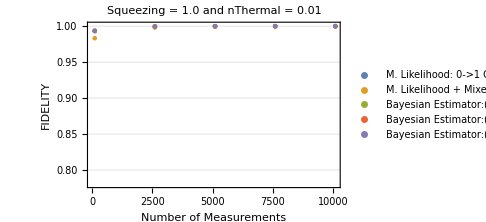
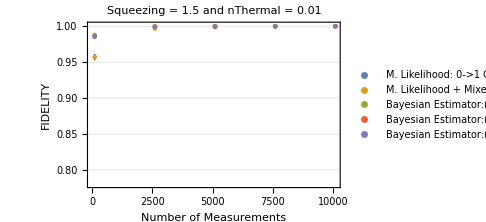
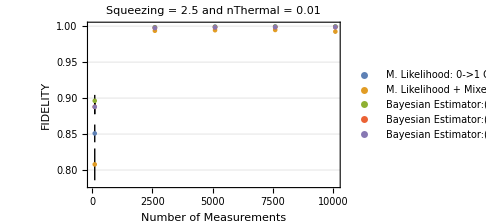

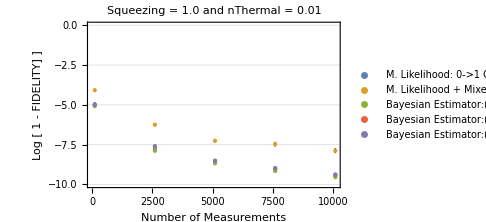
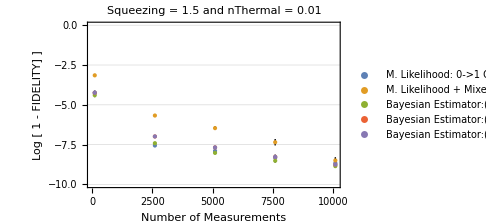
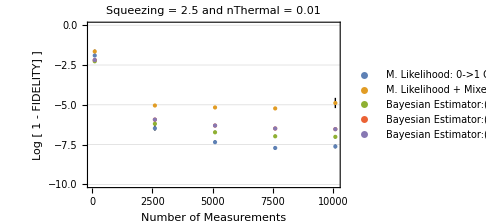

```mathematica
{ListPlot[{meanTableS10W1[[2]],meanTableS10W3[[2]],meanTableS10W4[[2]],meanTableS10W5[[2]],meanTableS10W6[[2]]},PlotRange->{{0.78,1.001}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements","FIDELITY"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 1.0 and nThermal = 0.01",ImageSize->Medium,PlotLegends->Placed[{"M. Likelihood: 0->1 Count Fix","M. Likelihood + Mixed Dist.","Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.342}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]],

ListPlot[{meanTableS15W1[[2]] ,meanTableS15W3[[2]] ,meanTableS15W4[[2]],meanTableS15W5[[2]],meanTableS15W6[[2]]},PlotRange->{{0.78,1.001}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements","FIDELITY"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 1.5 and nThermal = 0.01",ImageSize->Medium,PlotLegends->Placed[{"M. Likelihood: 0->1 Count Fix","M. Likelihood + Mixed Dist.","Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.342}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]],

ListPlot[{meanTableS25W1[[2]],meanTableS25W3[[2]],meanTableS25W4[[2]],meanTableS25W5[[2]],meanTableS25W6[[2]]},PlotRange->{{0.78,1.001}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements","FIDELITY"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 2.5 and nThermal = 0.01",ImageSize->Medium,PlotLegends->Placed[{"M. Likelihood: 0->1 Count Fix","M. Likelihood + Mixed Dist.","Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.342}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]]}

(*Log Plot*)
{ListPlot[{Log[1-meanTableS10W1[[2]]],Log[1-meanTableS10W3[[2]]],Log[1-meanTableS10W4[[2]]],Log[1-meanTableS10W5[[2]]],Log[1-meanTableS10W6[[2]]]},PlotRange->{{-0.01,-10}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements"," Log [ 1 - FIDELITY] ]"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 1.0 and nThermal = 0.01",ImageSize->Medium,PlotStyle->PointSize[Medium], PlotLegends->Placed[{"M. Likelihood: 0->1 Count Fix","M. Likelihood + Mixed Dist.","Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.74}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]],

ListPlot[{Log[1-meanTableS15W1[[2]] ],Log[1-meanTableS15W3[[2]] ],Log[1-meanTableS15W4 [[2]]],Log[1-meanTableS15W5[[2]]],Log[1-meanTableS15W6[[2]]]},PlotRange->{{-0.01,-10}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements"," Log [ 1 - FIDELITY] ]"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 1.5 and nThermal = 0.01",ImageSize->Medium,PlotStyle->PointSize[Medium],PlotLegends->Placed[{"M. Likelihood: 0->1 Count Fix","M. Likelihood + Mixed Dist.","Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.74}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]],

ListPlot[{Log[1-meanTableS25W1[[2]]],Log[1-meanTableS25W3[[2]]],Log[1-meanTableS25W4[[2]]],Log[1-meanTableS25W5[[2]]],Log[1-meanTableS25W6[[2]]]},PlotRange->{{-0.01,-10}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements"," Log [ 1 - FIDELITY] ]"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 2.5 and nThermal = 0.01",ImageSize->Medium,PlotStyle->PointSize[Medium],PlotLegends->Placed[{"M. Likelihood: 0->1 Count Fix","M. Likelihood + Mixed Dist.","Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.74}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]]}
```

## SECTION 6: Plots2

```mathematica
(*{ListPlot[{meanTableS10W4[[2]],meanTableS10W5[[2]],meanTableS10W6[[2]]},PlotRange->{{0.992,1.00}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements","FIDELITY"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 1.0 and nThermal = 0.01",ImageSize->Medium,PlotLegends->Placed[{"Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.342}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]],

ListPlot[{meanTableS15W4[[2]],meanTableS15W5[[2]],meanTableS15W6[[2]]},PlotRange->{{0.980,1.00}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements","FIDELITY"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 1.5 and nThermal = 0.01",ImageSize->Medium,PlotLegends->Placed[{"Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.342}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]],

ListPlot[{meanTableS25W4[[2]],meanTableS25W5[[2]],meanTableS25W6[[2]]},PlotRange->{{0.85,1.001}},DataRange->{100,10100},Frame->True,FrameLabel->{"Number of Measurements","FIDELITY"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 2.5 and nThermal = 0.01",ImageSize->Medium,PlotLegends->Placed[{"Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.342}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8]]}*)

(*Log Plot*)
(*Show[{ListLinePlot[{Log[1-meanTableS10W4[[2]]],Log[1-meanTableS10W5[[2]]],Log[1-meanTableS10W6[[2]]]},PlotRange->{{-2,-10}},DataRange->{100,10100},Frame->True,FrameLabel->{"Measurements"," Log ( 1 - Fidelity )"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 1.0 and nThermal = 0.01",ImageSize->Medium,PlotStyle->{{LightBlue,Dashing[Tiny]},{Lighter[Orange],Dashing[Tiny]},{Lighter[Green],Dashing[Tiny]}}, PlotLegends->Placed[{"Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.70}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8],PlotMarkers->{"●",6}],

ListLinePlot[{Log[1-meanTableS15W4 [[2]]],Log[1-meanTableS15W5[[2]]],Log[1-meanTableS15W6[[2]]]},PlotRange->{{-2,-10}},DataRange->{100,10100},Frame->True,FrameLabel->{"Measurements"," Log ( 1 - Fidelity )"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray, Dashed],PlotLabel->"Squeezing = 1.5 and nThermal = 0.01",ImageSize->Medium,PlotStyle->{{Blue,Dashing[Large]},{Orange,Dashing[Large]},{Green,Dashing[Large]}},PlotLegends->Placed[{"Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.70}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8],PlotMarkers->{"■",6}],

ListLinePlot[{Log[1-meanTableS25W4[[2]]],Log[1-meanTableS25W5[[2]]],Log[1-meanTableS25W6[[2]]]},PlotRange->{{-2,-10}},DataRange->{100,10100},Frame->True,FrameLabel->{"Measurements"," Log ( 1 - Fidelity )"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Squeezing = 2.5 and nThermal = 0.01",ImageSize->Medium,PlotStyle->{{Darker[Blue],Thickness[0.0001]},{Darker[Orange],Thickness[0.0001]},{Darker[Green],Thickness[0.0001]}},PlotLegends->Placed[{"Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.74}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->8],PlotMarkers->{"▲",6}],LabelStyle->Directive[Black,Bold],FrameTicks->True, FrameTicksStyle->Directive[Black,Bold]}]*)
```

```mathematica
GraphicsColumn[{ListPlot[{1-meanTableS10W4new,1-meanTableS10W5new,1-meanTableS10W6new,1-meanTableS10nWnew},PlotRange->{5*10^-5,0.2},DataRange->{1,101},Frame->True,FrameLabel->{None,"1 - <Fidelity>"},FrameTicksStyle->14,IntervalMarkersStyle->{Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Thickness[0.003]],Directive[RGBColor[0.996078431372549, 0.9, 0.09],Thickness[0.003]],Directive[RGBColor[0.5411764705882353, 0.78, 0.027450980392156862],Thickness[0.003]],Directive[RGBColor[0.996078431372549, 0.3, 0.027450980392156862],Thickness[0.003]]},GridLines->{None,Full},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,PlotStyle->{Bold,Thickness[0.0001]},LabelStyle->Directive[Black,16],PlotMarkers->{{"●",10},{"*",15},{"▲",11},{"■",10}},FrameTicks->{{Automatic,Automatic},{None,Automatic}},ScalingFunctions->"Log10"],
ListPlot[{1-meanTableS15W4new,1-meanTableS15W5new,1-meanTableS15W6new,1-meanTableS15nWnew},PlotRange->{5*10^-5,0.2},DataRange->{1,101},Frame->True,FrameLabel->{None,"1 - <Fidelity>"},FrameTicksStyle->14,IntervalMarkersStyle->{Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Thickness[0.003]],Directive[RGBColor[0.996078431372549, 0.9, 0.09],Thickness[0.003]],Directive[RGBColor[0.5411764705882353, 0.78, 0.027450980392156862],Thickness[0.003]],Directive[RGBColor[0.996078431372549, 0.3, 0.027450980392156862],Thickness[0.003]]},GridLines->{None,Full},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,PlotStyle->{Bold,Thickness[0.0001]},LabelStyle->Directive[Black,16],PlotMarkers->{{"●",11},{"*",16},{"▲",12},{"■",10}},FrameTicks->{{Automatic,Automatic},{None,Automatic}},ScalingFunctions->"Log10"],
ListPlot[{1-meanTableS25W4new,1-meanTableS25W5new,1-meanTableS25W6new,1-meanTableS25nWnew},PlotRange->{5*10^-5,0.2},DataRange->{1,101},Frame->True,FrameLabel->{"Measurements x 10","1 - <Fidelity>"},FrameTicksStyle->14,IntervalMarkersStyle->{Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Thickness[0.003]],Directive[RGBColor[0.996078431372549, 0.9, 0.09],Thickness[0.003]],Directive[RGBColor[0.5411764705882353, 0.78, 0.027450980392156862],Thickness[0.003]],Directive[RGBColor[0.996078431372549, 0.3, 0.027450980392156862],Thickness[0.003]]},GridLines->{None,Full},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,PlotStyle->{Bold,Thickness[0.0001]},LabelStyle->Directive[Black,16],PlotMarkers->{{"●",10},{"*",15},{"▲",11},{"■",10}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ScalingFunctions->"Log10"]},Spacings->-63.5]
```

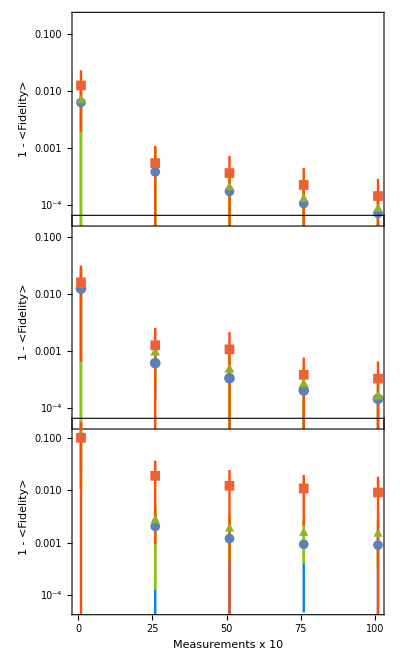

```mathematica
Short[ColorData[3,"ColorList"],3]
```

```mathematica
{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3, 0.027450980392156862],RGBColor[0.996078431372549, 0.9, 0.09],RGBColor[0.5411764705882353, 0.78, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}
```

```mathematica
ColorData[3]
```

ColorDataFunction[…]

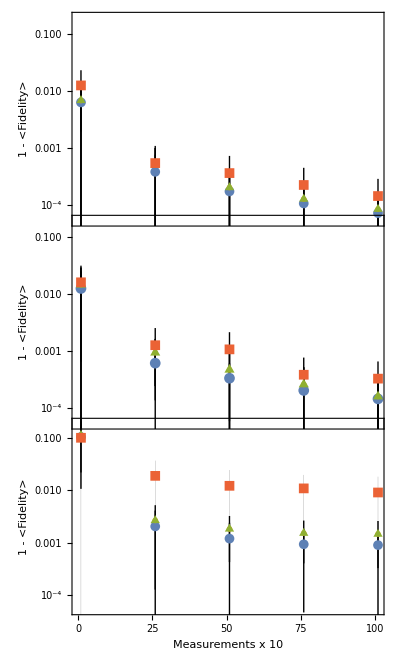

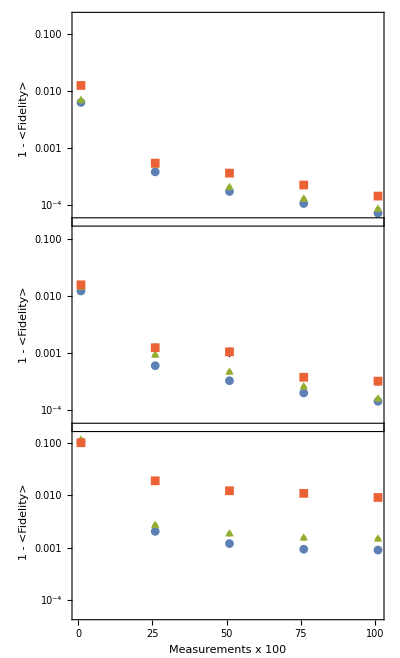

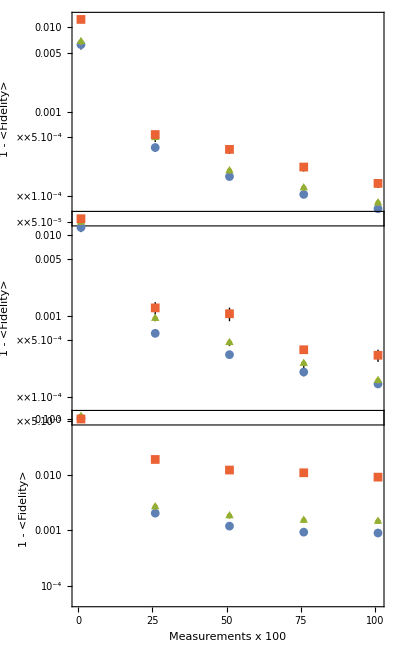

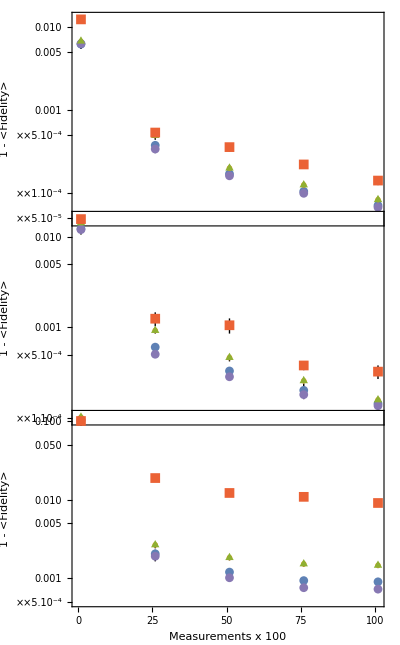

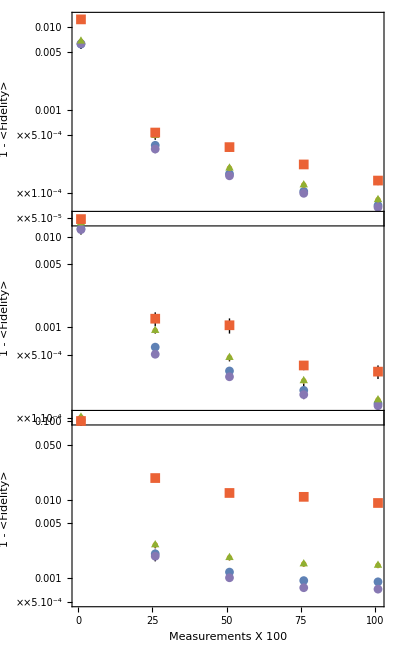

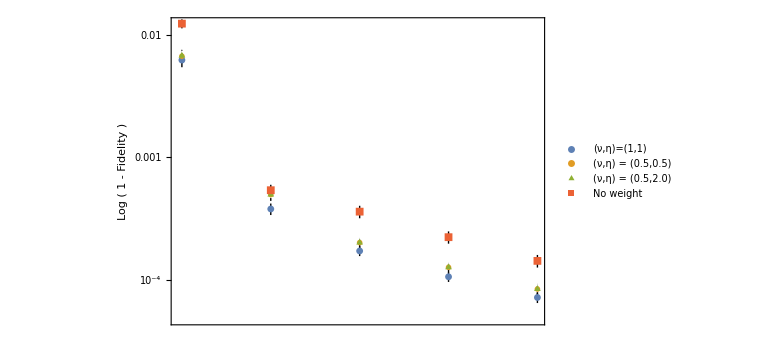

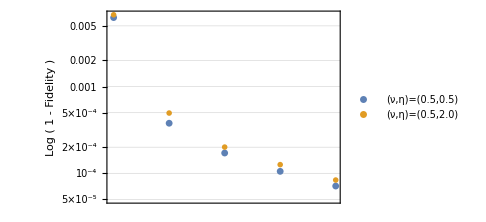

```mathematica
ListLogPlot[{1-meanTableS10W4[[2]],1-meanTableS10W5[[2]],1-meanTableS10W6[[2]],1-meanTableS10nW[[2]]},PlotRange->Full,DataRange->{1,101},Frame->True,FrameLabel->{None," Log ( 1 - Fidelity )"},FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,PlotStyle->{Dashed,Dashing[Tiny],Thickness[0.0001]},LabelStyle->Directive[Black,16],PlotMarkers->{{"●",7},{"*",12},{"▲",8},{"■",8}},FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotLegends->Placed[LineLegend[{Style["(ν,η)=(1,1)",14],Style["(ν,η) = (0.5,0.5)",14],Style["(ν,η) = (0.5,2.0)",14],Style["No weight",14]},LegendFunction->(Framed[#,Background->White]&)],{0.7,0.74}]]

ListLogPlot[{1-meanTableS10W4[[2]],1-meanTableS10W5[[2]],Log[1-meanTableS10W6[[2]]]},PlotRange->{{-1.7,-9.8}},DataRange->{100,10100},Frame->True,FrameLabel->{None," Log ( 1 - Fidelity )"},FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Medium,PlotStyle->{Dashed,Dashing[Tiny],Thickness[0.0001]},LabelStyle->Directive[Black,16],PlotMarkers->{{"●",7},{"*",12},{"▲",8}},FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotLegends->Placed[LineLegend[{"(ν,η)=(0.5,0.5)","(ν,η)=(0.5,2.0)"},LegendFunction->(Framed[#,Background->White]&)],Above]]
```

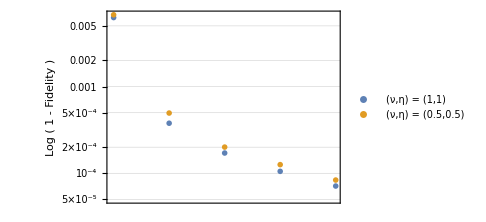

```mathematica
(ν,η)
```

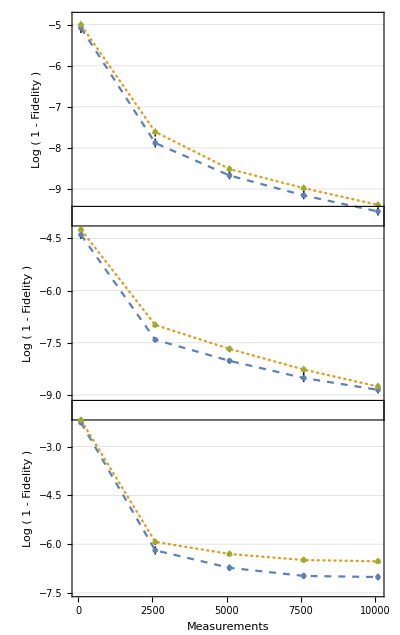

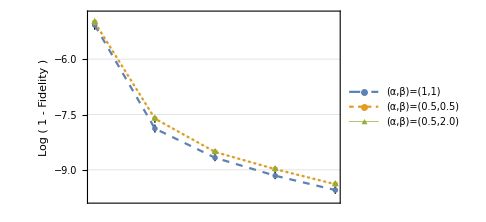
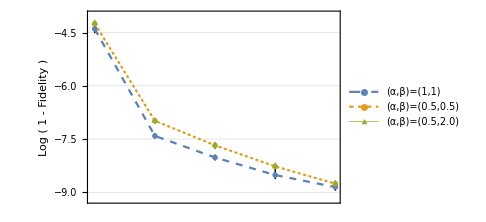
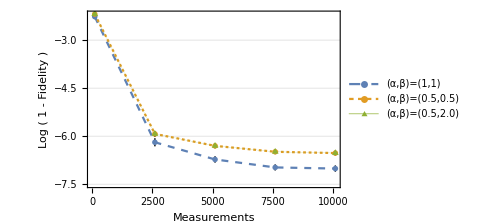

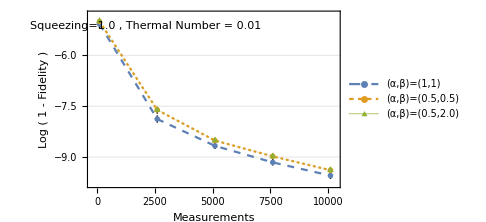
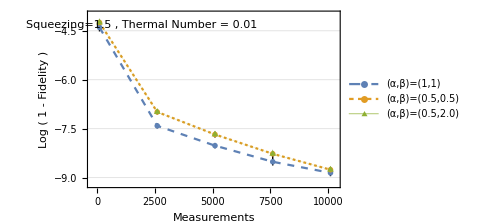
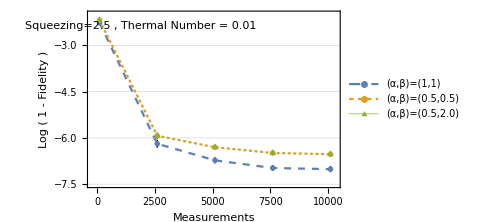

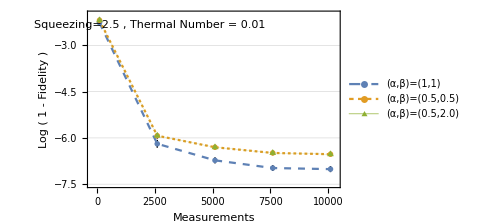

```mathematica
ListLinePlot[{Log[1-meanTableS25W4[[2]]],Log[1-meanTableS25W5[[2]]],Log[1-meanTableS25W6[[2]]]},PlotRange->{{-2,-7.5}},DataRange->{100,10100},Frame->True,FrameLabel->{"Measurements"," Log ( 1 - Fidelity )"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Medium,PlotStyle->{Dashed,Dashing[Tiny],Thickness[0.0001]},PlotLegends->Placed[{"(α,β)=(1,1)","(α,β)=(0.5,0.5)","(α,β)=(0.5,2.0)"},{0.7,0.74}],PlotMarkers->{{"*",16},{"*",12},{"▲",8}}]
```

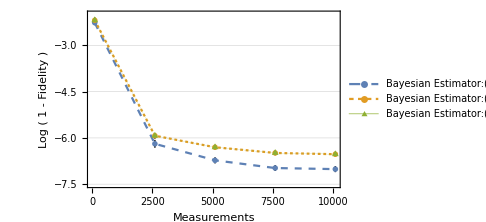

```mathematica
ListLinePlot[{Log[1-meanTableS25W4[[2]]],Log[1-meanTableS25W5[[2]]],Log[1-meanTableS25W6[[2]]]},PlotRange->{{-2,-7.5}},DataRange->{100,10100},Frame->True,FrameLabel->{"Measurements"," Log ( 1 - Fidelity )"},FrameTicksStyle->11,IntervalMarkersStyle->Black,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Medium,PlotStyle->{Dashed,Dashing[Tiny],Thickness[0.0001]},PlotLegends->Placed[{"Bayesian Estimator:(1,1)","Bayesian Estimator:(0.5,0.5)","Bayesian Estimator:(0.5,2.0)"},{0.7,0.74}],PlotMarkers->{{"*",16},{"*",12},{"▲",8}}]
```

```mathematica
meanTableS25W4[[2]]
```

{0.8960.008,0.997950.00026,0.998800.00012,0.999070.00009,0.999100.00009}

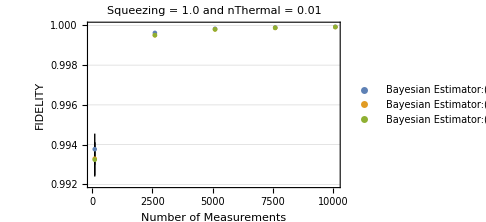
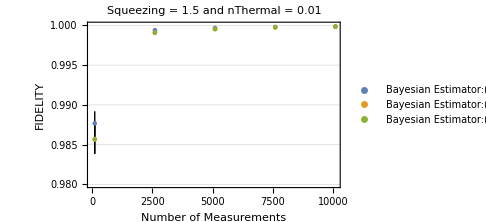
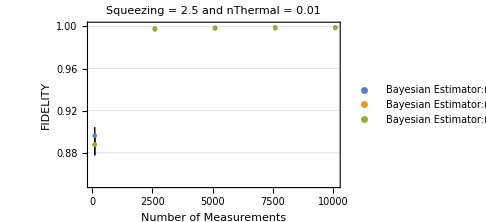

## SECTION 7a: Plots of Weights vs nFock

```mathematica
(*Plots of weights for 3 different states: Squeezing = 1.0, 1.5 and 2.5 and the same nThermal = 0.01
We consider the Log of the weights as the more appropriate plot
The table for a specific state has 5 columns: Each for a different mothod of calculating weights *)
(*Tables of frequencies: *)
freqtable251=relativeFreqDistTo20[σpp[2.5,nThermal],σqq[2.5,nThermal],100,NFockFinal];
freqtable252=relativeFreqDistTo20[σpp[2.5,nThermal],σqq[2.5,nThermal],1000,NFockFinal];
freqtable253=relativeFreqDistTo20[σpp[2.5,nThermal],σqq[2.5,nThermal],5000,NFockFinal];
```

```mathematica
(*Tables of weights(Log): *)
table251=Log[Table[
{
weight1[freqtable251,100,j-1],weight3[freqtable251,100,j-1],weight4[freqtable251,100,j-1],weight5[freqtable251,100,j-1],
weight6[freqtable251,100,j-1]
},
{j,1,21}],10];
table252=Log[Table[
{
weight1[freqtable252,1000,j-1],weight3[freqtable252,1000,j-1],weight4[freqtable252,1000,j-1],weight5[freqtable252,1000,j-1],
weight6[freqtable252,1000,j-1]
},
{j,1,21}],10];
table253=Log[Table[
{
weight1[freqtable253,5000,j-1],weight3[freqtable253,5000,j-1],weight4[freqtable253,5000,j-1],weight5[freqtable253,5000,j-1],
weight6[freqtable253,5000,j-1]
},
{j,1,21}],10];
```

```mathematica
(*Plots*)
```

```mathematica
SaveToCell[freqtable251];
SaveToCell[freqtable252];
SaveToCell[freqtable253];
```

```mathematica
freqtable253="data";
```

```mathematica
freqtable252="data";
```

```mathematica
freqtable251="data";
```

```mathematica
Subscript[ω,n]
ω
```

ω_n

ω

```mathematica
GraphicsColumn[{ListPlot[{table251[[All,3]],table251[[All,4]],table251[[All,5]]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotRange->{0.12,0.36},DataRange->{0,20},Frame->True,FrameLabel->{"",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black, 16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}],
(*For table 252*)
ListPlot[{table252[[All,3]],table252[[All,4]],table252[[All,5]]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},DataRange->{0,20},PlotRange->{0.12,0.36},Frame->True,FrameLabel->{"",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black, 16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}],
(*For table 253*)
ListPlot[{table253[[All,3]],table253[[All,4]],table253[[All,5]]},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},DataRange->{0,20},PlotRange->{0.12,0.36},Frame->True,FrameLabel->{"Fock Number",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black,16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}]},Spacings->-60]
```

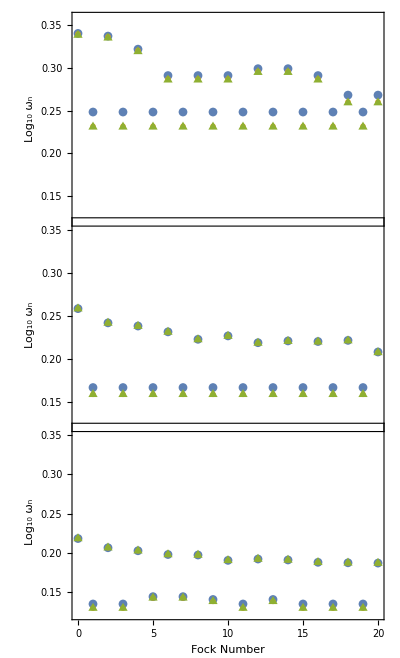

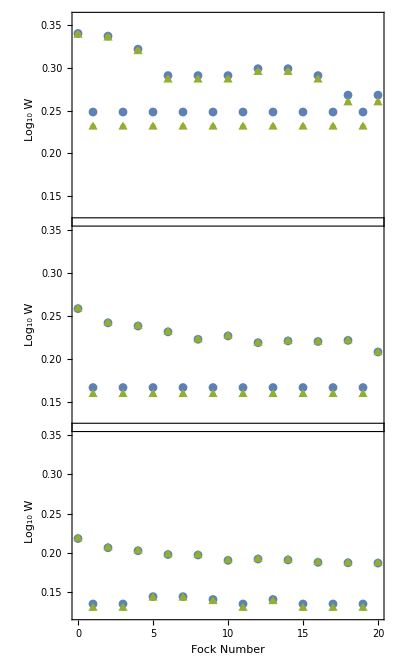

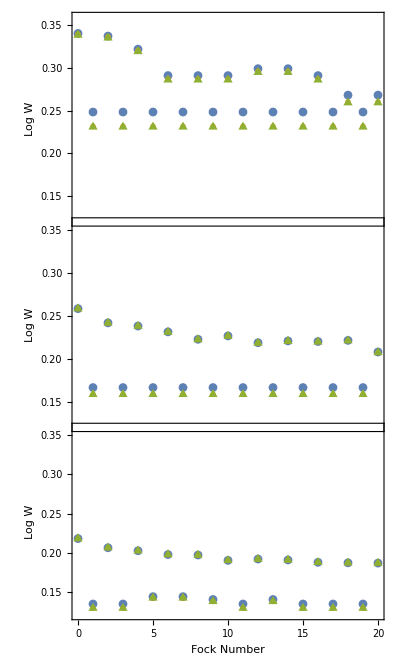

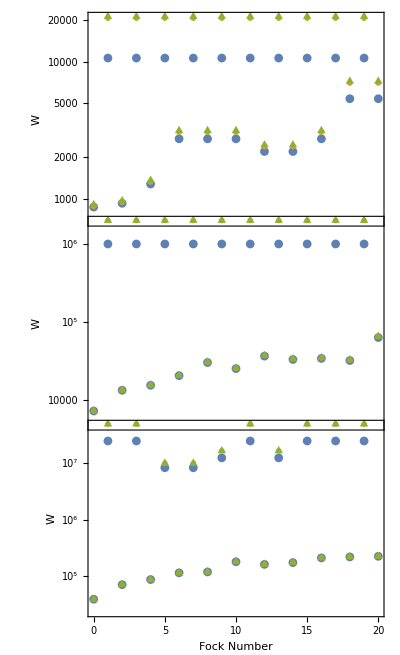

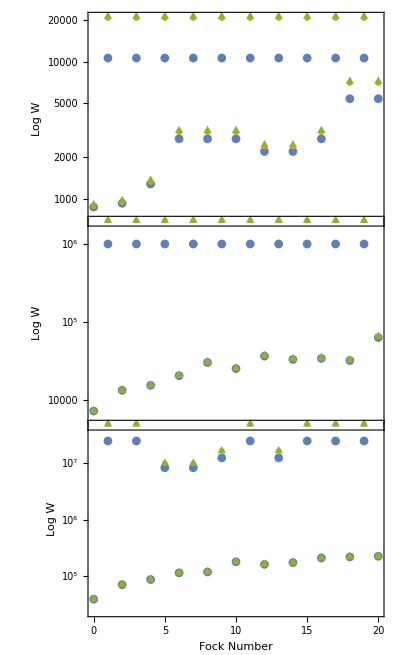

```mathematica
Log[table251[[All,3]]]
```

{6.76828,9.26955,6.83109,9.26955,7.15485,9.26955,7.91341,9.26955,7.91341,9.26955,7.91341,9.26955,7.70053,9.26955,7.70053,9.26955,7.91341,9.26955,8.58636,9.26955,8.58636}

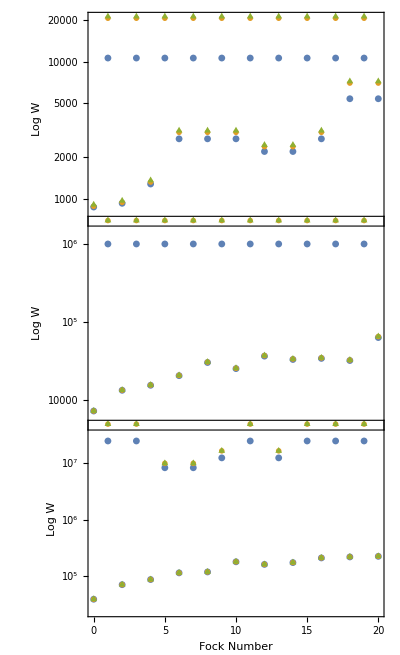

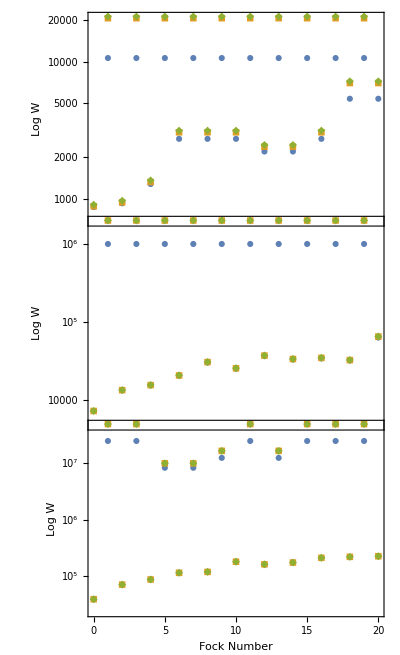

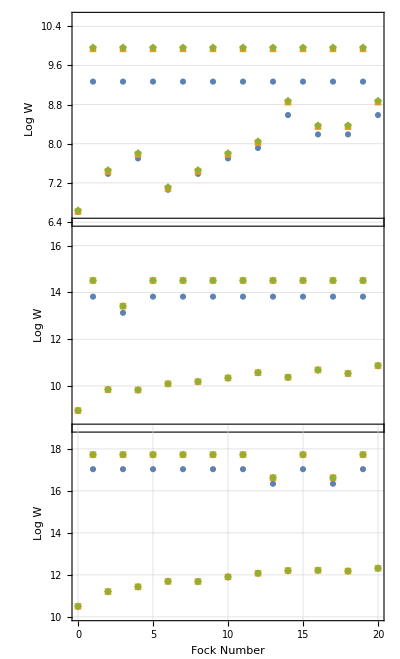

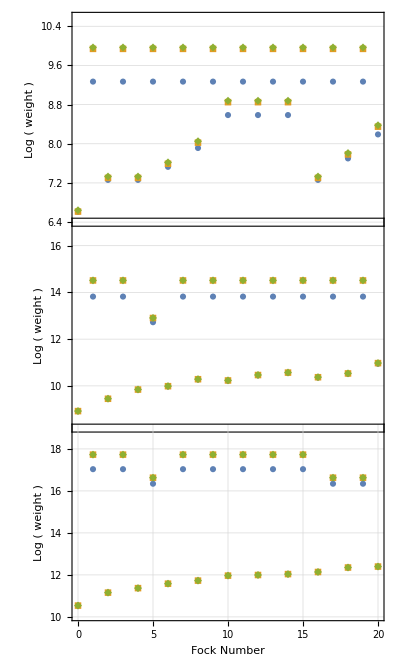

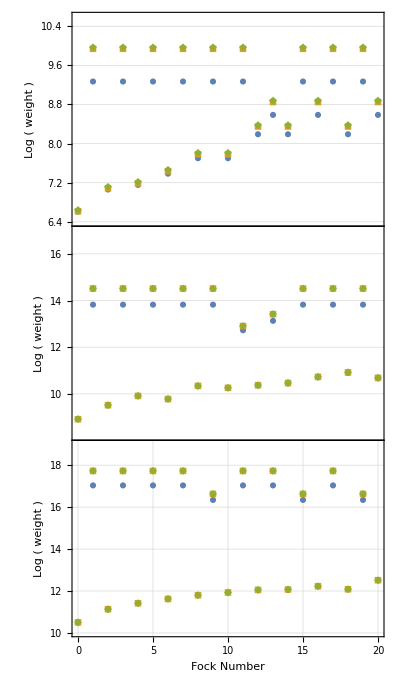

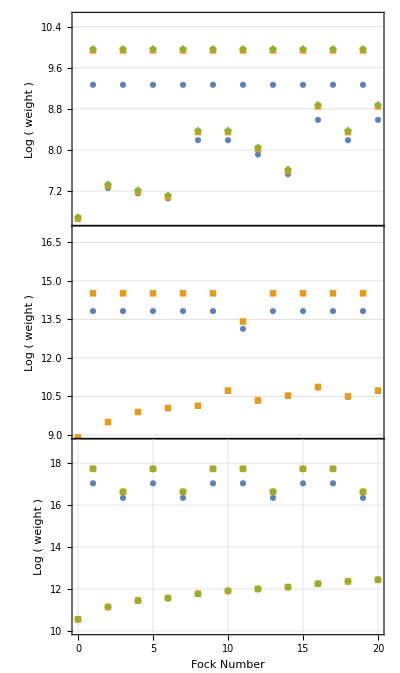

## SECTION 7b: Plots of Weights vs nFock

```mathematica
(*Plots of weights for 3 different states: Squeezing = 1.0, 1.5 and 2.5 and the same nThermal = 0.01*)
(*Tables of frequencies: *)
freqtable151=relativeFreqDistTo20[σpp[1.5,nThermal],σqq[1.5,nThermal],100,NFockFinal];
freqtable152=relativeFreqDistTo20[σpp[1.5,nThermal],σqq[1.5,nThermal],1000,NFockFinal];
freqtable153=relativeFreqDistTo20[σpp[1.5,nThermal],σqq[1.5,nThermal],10000,NFockFinal];
(*Tables of frequencies: *)
freqtable101=relativeFreqDistTo20[σpp[1.0,nThermal],σqq[1.0,nThermal],100,NFockFinal];
freqtable102=relativeFreqDistTo20[σpp[1.0,nThermal],σqq[1.0,nThermal],1000,NFockFinal];
freqtable103=relativeFreqDistTo20[σpp[1.0,nThermal],σqq[1.0,nThermal],10000,NFockFinal];
```

```mathematica
(*Tables of frequencies: *)
freqtable151c=relativeFreqDistTo20[σpp[1.5,0.1],σqq[1.5,0.1],100,NFockFinal];
freqtable152c=relativeFreqDistTo20[σpp[1.5,0.1],σqq[1.5,0.1],1000,NFockFinal];
freqtable153c=relativeFreqDistTo20[σpp[1.5,0.1],σqq[1.5,0.1],100000,NFockFinal];
(*Tables of frequencies: *)
freqtable101c=relativeFreqDistTo20[σpp[1.0,0.1],σqq[1.0,0.1],100,NFockFinal];
freqtable102c=relativeFreqDistTo20[σpp[1.0,0.1],σqq[1.0,0.1],1000,NFockFinal];
freqtable103c=relativeFreqDistTo20[σpp[1.0,0.1],σqq[1.0,0.1],10000,NFockFinal];
(*Tables of frequencies: *)
freqtable251c=relativeFreqDistTo20[σpp[2.5,0.1],σqq[2.5,0.1],100,NFockFinal];
freqtable252c=relativeFreqDistTo20[σpp[2.5,0.1],σqq[2.5,0.1],1000,NFockFinal];
freqtable253c=relativeFreqDistTo20[σpp[2.5,0.1],σqq[2.5,0.1],10000,NFockFinal];
```

```mathematica
(*Table of lists of log(weights) for different weight functions(shape parameters)*)
tableWeights[TABLE_]:=Log[Table[{weight1[TABLE,100,j-1],weight3[TABLE,100,j-1],weight4[TABLE,100,j-1],weight5[TABLE,100,j-1],weight6[TABLE,100,j-1]},{j,1,21}],10];
```

```mathematica
(*Tables of weights(Log): *)
table151=tableWeights[freqtable151];
table152=tableWeights[freqtable152];
table153=tableWeights[freqtable153];
(*Tables of weights(Log): *)
table101=tableWeights[freqtable101];
table102=tableWeights[freqtable102];
table103=tableWeights[freqtable103];
(*Tables of weights(Log): *)
table151c=tableWeights[freqtable151c];
table152c=tableWeights[freqtable152c];
table153c=tableWeights[freqtable153c];
(*Tables of weights(Log): *)
table101c=tableWeights[freqtable101c];
table102c=tableWeights[freqtable102c];
table103c=tableWeights[freqtable103c];
(*Tables of weights(Log): *)
table251c=tableWeights[freqtable251c];
table252c=tableWeights[freqtable252c];
table253c=tableWeights[freqtable253c];
```

```mathematica
(*Plots*)
```

```mathematica
SaveToCell[freqtable151];
SaveToCell[freqtable152];
SaveToCell[freqtable153];
```

```mathematica
Subscript[ω,n]
ω
```

ω_n

ω

```mathematica
(*Plot Function for 3 number of measurements. It plots log of weights for each Fock number, for different shape parameters*)
Clear[plotWeightsComparison]
plotWeightsComparison[TABLE1_,TABLE2_,TABLE3_]:=GraphicsColumn[{ListPlot[{TABLE1[[All,3]],TABLE1[[All,4]],TABLE1[[All,5]]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotRange->{0.12,0.385},DataRange->{0,20},Frame->True,FrameLabel->{"",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black, 16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}],
(*For table 252*)
ListPlot[{TABLE2[[All,3]],TABLE2[[All,4]],TABLE2[[All,5]]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},DataRange->{0,20},PlotRange->{0.12,0.385},Frame->True,FrameLabel->{"",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black, 16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}],
(*For table 253*)
ListPlot[{TABLE3[[All,3]],TABLE3[[All,4]],TABLE3[[All,5]]},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},DataRange->{0,20},PlotRange->{0.12,0.385},Frame->True,FrameLabel->{"Fock Number",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black,16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}]},Spacings->-60];
```

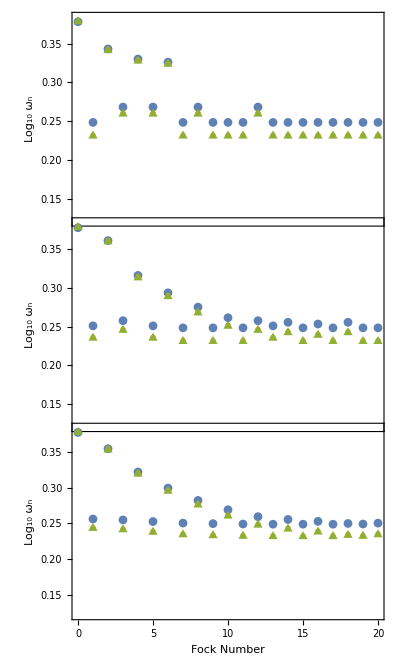
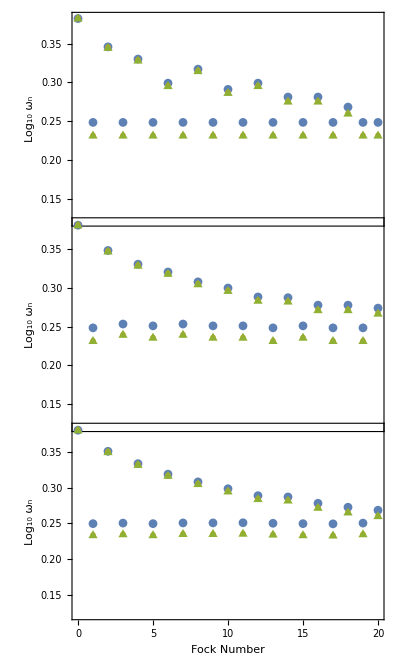
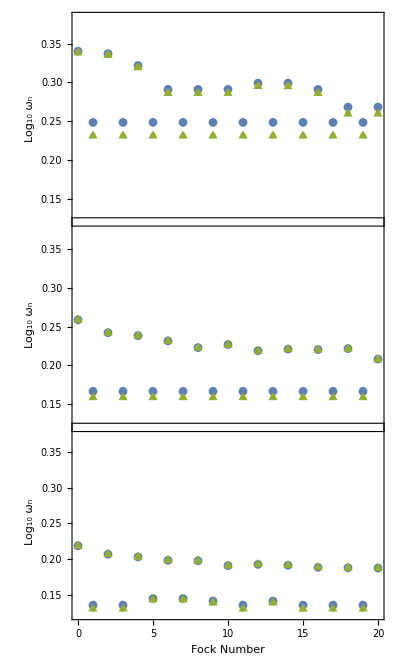

```mathematica
{plotWeightsComparison[table101,table102,table103],
plotWeightsComparison[table151,table152,table153],
plotWeightsComparison[table251,table252,table253]}
{plotWeightsComparison[table101c,table102c,table103c],
plotWeightsComparison[table151c,table152c,table153c],
plotWeightsComparison[table251c,table252c,table253c]}
```

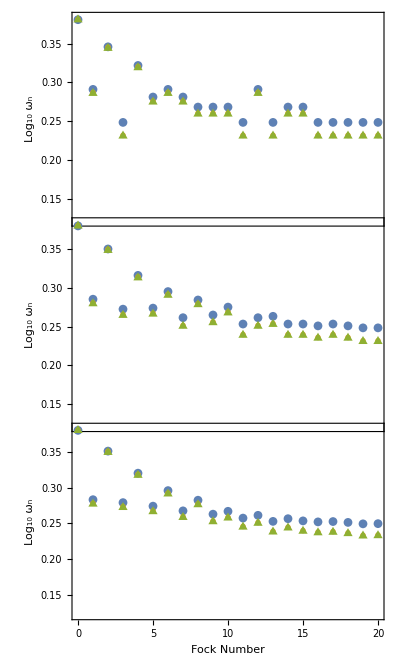
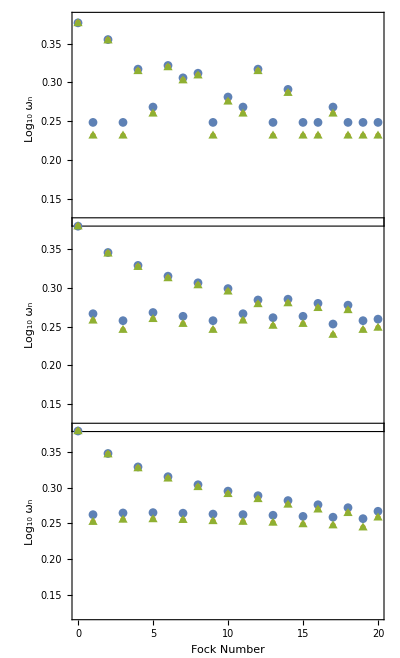
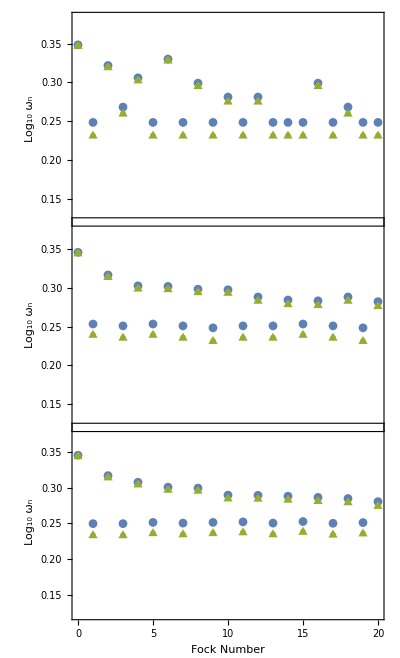

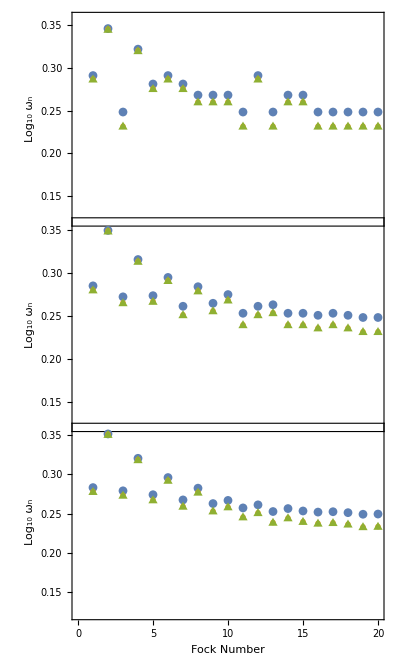
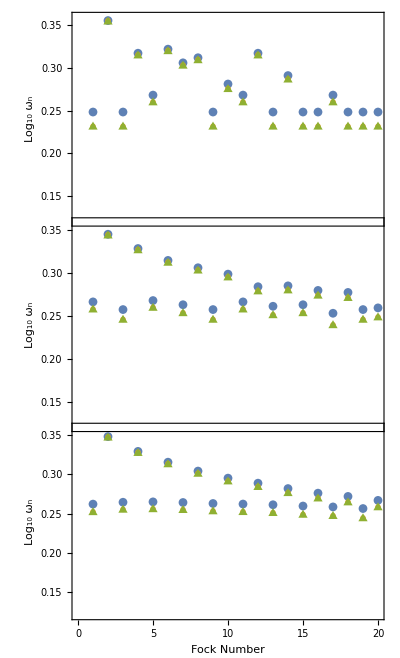
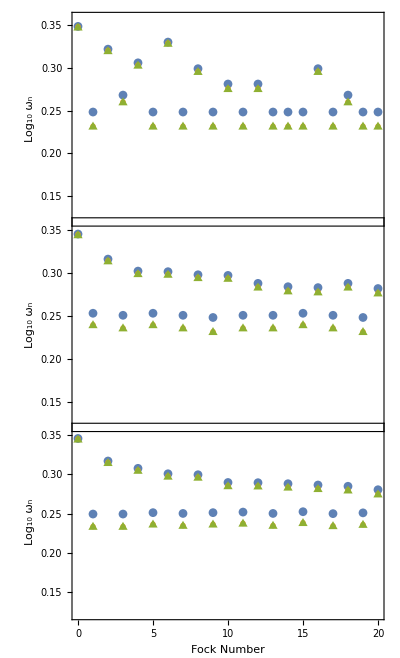

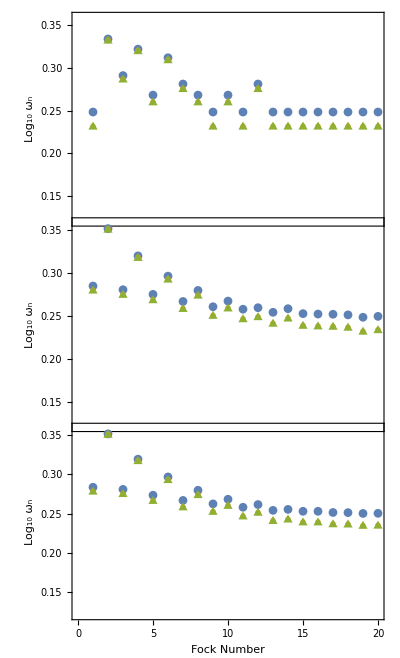
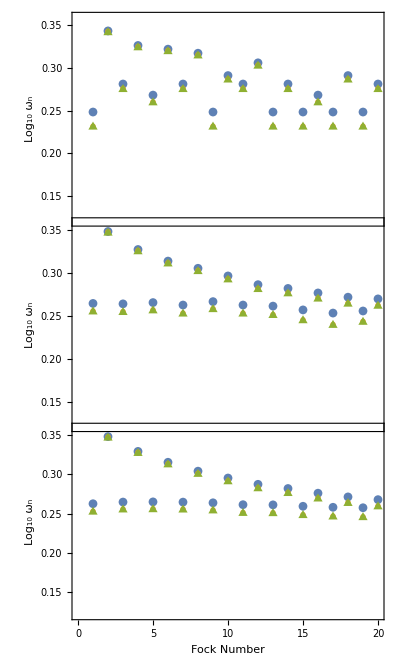

## SECTION 7c: Plots of Weights vs nFock

```mathematica
(*Plots of weights for 3 different states: Squeezing = 1.0, 1.5 and 2.5 and the same nThermal = 0.01
We consider the Log of the weights as the more appropriate plot
The table for a specific state has 5 columns: Each for a different mothod of calculating weights *)
(*Tables of frequencies: *)
freqtable251=relativeFreqDistTo20[σpp[2.5,nThermal],σqq[2.5,nThermal],100,NFockFinal];
freqtable252=relativeFreqDistTo20[σpp[2.5,nThermal],σqq[2.5,nThermal],1000,NFockFinal];
freqtable253=relativeFreqDistTo20[σpp[2.5,nThermal],σqq[2.5,nThermal],5000,NFockFinal];
```

```mathematica
(*Tables of weights(Log): *)
table251=Log[Table[
{
weight1[freqtable251,100,j-1],weight3[freqtable251,100,j-1],weight4[freqtable251,100,j-1],weight5[freqtable251,100,j-1],
weight6[freqtable251,100,j-1]
},
{j,1,21}],10];
table252=Log[Table[
{
weight1[freqtable252,1000,j-1],weight3[freqtable252,1000,j-1],weight4[freqtable252,1000,j-1],weight5[freqtable252,1000,j-1],
weight6[freqtable252,1000,j-1]
},
{j,1,21}],10];
table253=Log[Table[
{
weight1[freqtable253,5000,j-1],weight3[freqtable253,5000,j-1],weight4[freqtable253,5000,j-1],weight5[freqtable253,5000,j-1],
weight6[freqtable253,5000,j-1]
},
{j,1,21}],10];
```

```mathematica
(*Plots*)
```

```mathematica
SaveToCell[freqtable251];
SaveToCell[freqtable252];
SaveToCell[freqtable253];
```

```mathematica
freqtable253="data";
```

```mathematica
freqtable252="data";
```

```mathematica
freqtable251="data";
```

```mathematica
Subscript[ω,n]
ω
```

ω_n

ω

```mathematica
GraphicsColumn[{ListPlot[{table251[[All,3]],table251[[All,4]],table251[[All,5]]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotRange->{0.12,0.36},DataRange->{0,20},Frame->True,FrameLabel->{"",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black, 16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}],
(*For table 252*)
ListPlot[{table252[[All,3]],table252[[All,4]],table252[[All,5]]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},DataRange->{0,20},PlotRange->{0.12,0.36},Frame->True,FrameLabel->{"",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black, 16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}],
(*For table 253*)
ListPlot[{table253[[All,3]],table253[[All,4]],table253[[All,5]]},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},DataRange->{0,20},PlotRange->{0.12,0.36},Frame->True,FrameLabel->{"Fock Number",Subscript[Log,10]"ω_n"},LabelStyle->Directive[Black,16],FrameTicks->True, FrameTicksStyle->14,IntervalMarkersStyle->Black,GridLines->{None,Full},GridLinesStyle->Directive[Gray, Dashed],ImageSize->Large,PlotMarkers->{{"●",9},{"*",15},{"▲",11}}]},Spacings->-60]
```

```mathematica
Log[table251[[All,3]]]
```

{6.76828,9.26955,6.83109,9.26955,7.15485,9.26955,7.91341,9.26955,7.91341,9.26955,7.91341,9.26955,7.70053,9.26955,7.70053,9.26955,7.91341,9.26955,8.58636,9.26955,8.58636}